```mathematica
SymbolsForPartsLevel4[partList_,filter_:Null]:=Block[
{
edges={},
nodes=Length[Flatten[First[partList]]]
},
If[filter==Null,filter=SymbolLevel[#]==4&];
Table[
edges=Join[edges,EdgeList[GraphComplement[GraphFromSets[part]]]],
{part,partList}];
Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[edges]]], filter]
]
```

```mathematica
ShowGraphForPartsLevel4[partList_]:=Block[
{
edges={},
nodes=Length[Flatten[First[partList]]]
},
Table[
edges=Join[edges,EdgeList[GraphComplement[GraphFromSets[part]]]],
{part,partList}];
Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[edges]]], SymbolLevel[#]==4&]
]
```

```mathematica
Table[First[QuadrilateralsWithPattern[7,k]],{k,5}]//ShowGraphForPartsLevel4
```

{v1x26x35x47,v1x247x35x6,v16x2x35x47,v16x27x35x4,v16x25x3x47,v16x25x37x4,v16x247x3x5,v16x24x37x5,v16x24x35x7,v14x27x35x6,v14x26x37x5,v14x26x35x7,v14x25x37x6,v13x26x47x5,v13x25x47x6,v13x247x5x6}

```mathematica
Table[First[QuadrilateralsWithPattern[7,k]],{k,5}]//ShowGraphForPartsLevel4
```

{v1x26x35x47,v1x247x35x6,v16x2x35x47,v16x27x35x4,v16x25x3x47,v16x25x37x4,v16x247x3x5,v16x24x37x5,v16x24x35x7,v14x27x35x6,v14x26x37x5,v14x26x35x7,v14x25x37x6,v13x26x47x5,v13x25x47x6,v13x247x5x6}

```mathematica
SymbolPartitionHasPattern[s1_,s2_]:=PartitionHasPattern[SymbolToSets[s1],SymbolToSets[s2]]
```

```mathematica
ShowSol2[sol_]:=Block[
{
start = Select[sol[[1]],MemberQ[sol[[2]],SymbolToSets[#]]&],
other = Select[sol[[1]],!MemberQ[sol[[2]],SymbolToSets[#]]&]
},
ShowGraphs[start,Directive[Dotted,Thick,Orange]&]->
ShowGraphs[other,If[HasQuadrilateralPattern[#],Red,Darker[Green]]&]
]
```

```mathematica
Experiment123[nodes_]:=Block[
{
lowerPatterns=Association[],
higherPartitions=Association[],
lowerSolutionSymbols,
higherSolutionSymbols,
higherToLower=Association[],
lowerToHigher=Association[]
},
Table[
lowerPatterns[k]=First[QuadrilateralsWithPattern[nodes,k]];
higherPartitions[k]=Sort[Select[QuadrilateralsWithPattern[nodes+1,k],PartitionHasPattern[#,lowerPatterns[k]]&]]
,
{k,5}
];
lowerSolutionSymbols=SymbolsForPartsLevel4[Values[lowerPatterns]];
Flatten[
Table[
Table[
Table[
Table[
Table[
higherSolutionSymbols=ShowGraphForPartsLevel4[{part1,part2,part3,part4,part5}];
(* compute higherToLower *)
Table[
higherToLower[high]={};
Table[If[SymbolPartitionHasPattern[high,low],
AppendTo[higherToLower[high],low]
]

,{low,lowerSolutionSymbols}]
,{high,higherSolutionSymbols}];

(* compute lowerToHigher *)
Table[
lowerToHigher[low]={};
Table[If[SymbolPartitionHasPattern[high,low],
AppendTo[lowerToHigher[low],high]
]
,{high,higherSolutionSymbols}]
,{low,lowerSolutionSymbols}];

{"lowerToHigher",lowerToHigher,
"higherToLower",higherToLower,
"lowerToHigher empty",
Table[
GraphFromSymbol[key]
,
{key,Select[Keys[lowerToHigher],lowerToHigher[#]=={}&]}
],

"higherToLower empty",
Table[
GraphFromSymbol[key]
,
{key,Select[Keys[higherToLower],higherToLower[#]=={}&]}
]
}
,
{part5,Take[higherPartitions[5],-1]}
],
{part4,Take[higherPartitions[4],-1]}
],
{part3,Take[higherPartitions[3],-1]}
],
{part2,Take[higherPartitions[2],-1]}
],
{part1,Take[higherPartitions[1],-1]}
],
5]
]
```

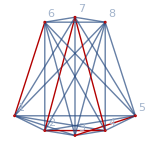
{lowerToHigher,<|v1x26x35x47→{v18x26x35x47},v1x247x35x6→{v1x247x35x68,v18x247x35x6},v16x2x35x47→{v168x2x35x47},v16x27x35x4→{v168x27x35x4,v16x27x35x48},v16x25x3x47→{v168x25x3x47,v16x25x38x47},v16x25x37x4→{v168x25x37x4,v16x25x37x48},v16x247x3x5→{v168x247x3x5,v16x247x38x5},v16x24x37x5→{v168x24x37x5},v16x24x35x7→{v168x24x35x7},v14x27x35x6→{v148x27x35x6,v14x27x35x68},v14x26x37x5→{v148x26x37x5},v14x26x35x7→{v148x26x35x7},v14x25x37x6→{v148x25x37x6,v14x25x37x68},v13x26x47x5→{v138x26x47x5},v13x25x47x6→{v138x25x47x6,v13x25x47x68},v13x247x5x6→{v138x247x5x6,v13x247x5x68}|>,higherToLower,<|v1x247x35x68→{v1x247x35x6},v18x26x35x47→{v1x26x35x47},v18x247x35x6→{v1x247x35x6},v168x2x35x47→{v16x2x35x47},v168x27x35x4→{v16x27x35x4},v16x27x35x48→{v16x27x35x4},v168x25x3x47→{v16x25x3x47},v16x25x38x47→{v16x25x3x47},v168x25x37x4→{v16x25x37x4},v16x25x37x48→{v16x25x37x4},v168x247x3x5→{v16x247x3x5},v16x247x38x5→{v16x247x3x5},v168x24x37x5→{v16x24x37x5},v168x24x35x7→{v16x24x35x7},v16x247x35x8→{},v148x27x35x6→{v14x27x35x6},v14x27x35x68→{v14x27x35x6},v148x26x37x5→{v14x26x37x5},v148x26x35x7→{v14x26x35x7},v148x25x37x6→{v14x25x37x6},v14x25x37x68→{v14x25x37x6},v138x26x47x5→{v13x26x47x5},v138x25x47x6→{v13x25x47x6},v13x25x47x68→{v13x25x47x6},v138x247x5x6→{v13x247x5x6},v13x247x5x68→{v13x247x5x6}|>,lowerToHigher empty,{},higherToLower empty,{-Graphics-}}

```mathematica
Experiment123[7]
```

```mathematica
Experiment124[nodes_]:=Block[
{
lowerPatterns=Association[],
higherPartitions=Association[],
lowerSolutionSymbols,
higherSolutionSymbols,
higherToLower=Association[],
lowerToHigher=Association[]
},
Table[
lowerPatterns[k]=First[QuadrilateralsWithPattern[nodes,k]];
higherPartitions[k]=Sort[Select[QuadrilateralsWithPattern[nodes+1,k],PartitionHasPattern[#,lowerPatterns[k]]&]]
,
{k,5}
];
lowerSolutionSymbols=SymbolsForPartsLevel4[Values[lowerPatterns]];
Flatten[
Table[
Table[
Table[
Table[
Table[
higherSolutionSymbols=ShowGraphForPartsLevel4[{part1,part2,part3,part4,part5}];
(* compute higherToLower *)
Table[
higherToLower[high]={};
Table[If[SymbolPartitionHasPattern[high,low],
AppendTo[higherToLower[high],low]
]

,{low,lowerSolutionSymbols}]
,{high,higherSolutionSymbols}];

(* compute lowerToHigher *)
Table[
lowerToHigher[low]={};
Table[If[SymbolPartitionHasPattern[high,low],
AppendTo[lowerToHigher[low],high]
]
,{high,higherSolutionSymbols}]
,{low,lowerSolutionSymbols}];

Select[Keys[lowerToHigher],lowerToHigher[#]=={}&]=={}
,
{part5,Take[higherPartitions[5],1]}
],
{part4,Take[higherPartitions[4],1]}
],
{part3,Take[higherPartitions[3],1]}
],
{part2,Take[higherPartitions[2],1]}
],
{part1,Take[higherPartitions[1],1]}
],
5]
]
```

```mathematica
Experiment124[8]
```

{True}

```mathematica
SeeWhichHighDontComeFromLow[nodes_]:=Block[
{
lowerPatterns=Association[],
higherPartitions=Association[],
lowerSolutionSymbols,
higherSolutionSymbols,
higherToLower=Association[],
lowerToHigher=Association[]
},
Table[
lowerPatterns[k]=First[QuadrilateralsWithPattern[nodes,k]];
higherPartitions[k]=Sort[Select[QuadrilateralsWithPattern[nodes+1,k],PartitionHasPattern[#,lowerPatterns[k]]&]]
,
{k,5}
];
lowerSolutionSymbols=SymbolsForPartsLevel4[Values[lowerPatterns],True&];
Flatten[
Table[
Table[
Table[
Table[
Table[
higherSolutionSymbols=SymbolsForPartsLevel4[{part1,part2,part3,part4,part5},True&];
(* compute higherToLower *)
Table[
higherToLower[high]={};
Table[If[SymbolPartitionHasPattern[high,low],
AppendTo[higherToLower[high],low]
]

,{low,lowerSolutionSymbols}]
,{high,higherSolutionSymbols}];

(* compute lowerToHigher *)
Table[
lowerToHigher[low]={};
Table[If[SymbolPartitionHasPattern[high,low],
AppendTo[lowerToHigher[low],high]
]
,{high,higherSolutionSymbols}]
,{low,lowerSolutionSymbols}];
Print[lowerSolutionSymbols];

Print[Sort[Tally[Map[SymbolLevel,lowerSolutionSymbols]]]];
Print[higherSolutionSymbols];

Print[Sort[Tally[Map[SymbolLevel,higherSolutionSymbols]]]];
Select[Keys[higherToLower],higherToLower[#]=={}&];
Print[higherToLower];

Print[lowerToHigher];
Print[Table[{k,Length[lowerToHigher[k]],lowerToHigher[k]},{k,Keys[lowerToHigher]}]];
,
{part5,Take[higherPartitions[5],2]}
],
{part4,Take[higherPartitions[4],1]}
],
{part3,Take[higherPartitions[3],1]}
],
{part2,Take[higherPartitions[2],1]}
],
{part1,Take[higherPartitions[1],1]}
],
5]
]
```

```mathematica
SeeWhichHighDontComeFromLow[8]
```

{v1x2x3x4x5x6x7x8,v1x2x3x4x58x6x7,v1x2x3x48x5x6x7,v1x2x3x47x5x6x8,v1x2x3x47x58x6,v1x2x37x4x5x6x8,v1x2x37x4x58x6,v1x2x37x48x5x6,v1x2x35x4x6x7x8,v1x2x35x48x6x7,v1x2x35x47x6x8,v1x27x3x4x5x6x8,v1x27x3x4x58x6,v1x27x3x48x5x6,v1x27x35x4x6x8,v1x27x35x48x6,v1x26x3x4x5x7x8,v1x26x3x4x58x7,v1x26x3x48x5x7,v1x26x3x47x5x8,v1x26x3x47x58,v1x26x37x4x5x8,v1x26x37x4x58,v1x26x37x48x5,v1x26x35x4x7x8,v1x26x35x48x7,v1x26x35x47x8,v1x25x3x4x6x7x8,v1x25x3x48x6x7,v1x25x3x47x6x8,v1x25x37x4x6x8,v1x25x37x48x6,v1x24x3x5x6x7x8,v1x247x3x5x6x8,v1x24x3x58x6x7,v1x247x3x58x6,v1x24x37x5x6x8,v1x24x37x58x6,v1x24x35x6x7x8,v1x247x35x6x8,v16x2x3x4x5x7x8,v16x2x3x4x58x7,v16x2x3x48x5x7,v16x2x3x47x5x8,v16x2x3x47x58,v16x2x37x4x5x8,v16x2x37x4x58,v16x2x37x48x5,v16x2x35x4x7x8,v16x2x35x48x7,v16x2x35x47x8,v16x27x3x4x5x8,v16x27x3x4x58,v16x27x3x48x5,v16x27x35x4x8,v16x27x35x48,v16x25x3x4x7x8,v16x25x3x48x7,v16x25x3x47x8,v16x25x37x4x8,v16x25x37x48,v16x24x3x5x7x8,v16x247x3x5x8,v16x24x3x58x7,v16x247x3x58,v16x24x37x5x8,v16x24x37x58,v16x24x35x7x8,v16x247x35x8,v14x2x3x5x6x7x8,v14x2x3x58x6x7,v14x2x37x5x6x8,v14x2x37x58x6,v14x2x35x6x7x8,v14x27x3x5x6x8,v14x27x3x58x6,v14x27x35x6x8,v14x26x3x5x7x8,v14x26x3x58x7,v14x26x37x5x8,v14x26x37x58,v14x26x35x7x8,v14x25x3x6x7x8,v14x25x37x6x8,v13x2x4x5x6x7x8,v13x2x4x58x6x7,v13x2x48x5x6x7,v13x2x47x5x6x8,v13x2x47x58x6,v13x27x4x5x6x8,v13x27x4x58x6,v13x27x48x5x6,v13x26x4x5x7x8,v13x26x4x58x7,v13x26x48x5x7,v13x26x47x5x8,v13x26x47x58,v13x25x4x6x7x8,v13x25x48x6x7,v13x25x47x6x8,v13x24x5x6x7x8,v13x247x5x6x8,v13x24x58x6x7,v13x247x58x6}

{{4,8},{5,42},{6,41},{7,12},{8,1}}

{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x59x6x7x8,v1x2x3x4x58x6x7x9,v1x2x3x4x589x6x7,v1x2x3x49x5x6x7x8,v1x2x3x49x58x6x7,v1x2x3x48x5x6x7x9,v1x2x3x489x5x6x7,v1x2x3x48x59x6x7,v1x2x3x47x5x6x8x9,v1x2x3x47x5x6x89,v1x2x3x47x59x6x8,v1x2x3x47x58x6x9,v1x2x3x47x589x6,v1x2x37x4x5x6x8x9,v1x2x37x4x5x6x89,v1x2x37x4x59x6x8,v1x2x37x4x58x6x9,v1x2x37x4x589x6,v1x2x37x49x5x6x8,v1x2x37x49x58x6,v1x2x37x48x5x6x9,v1x2x37x489x5x6,v1x2x37x48x59x6,v1x2x35x4x6x7x8x9,v1x2x35x4x6x7x89,v1x2x35x49x6x7x8,v1x2x35x48x6x7x9,v1x2x35x489x6x7,v1x2x35x47x6x8x9,v1x2x35x47x6x89,v1x27x3x4x5x6x8x9,v1x27x3x4x5x6x89,v1x27x3x4x59x6x8,v1x27x3x4x58x6x9,v1x27x3x4x589x6,v1x27x3x49x5x6x8,v1x27x3x49x58x6,v1x27x3x48x5x6x9,v1x27x3x489x5x6,v1x27x3x48x59x6,v1x27x35x4x6x8x9,v1x27x35x4x6x89,v1x27x35x49x6x8,v1x27x35x48x6x9,v1x27x35x489x6,v1x26x3x4x5x7x8x9,v1x26x3x4x5x7x89,v1x26x3x4x59x7x8,v1x26x3x4x58x7x9,v1x26x3x4x589x7,v1x26x3x49x5x7x8,v1x26x3x49x58x7,v1x26x3x48x5x7x9,v1x26x3x489x5x7,v1x26x3x48x59x7,v1x26x3x47x5x8x9,v1x26x3x47x5x89,v1x26x3x47x59x8,v1x26x3x47x58x9,v1x26x3x47x589,v1x26x37x4x5x8x9,v1x26x37x4x5x89,v1x26x37x4x59x8,v1x26x37x4x58x9,v1x26x37x4x589,v1x26x37x49x5x8,v1x26x37x49x58,v1x26x37x48x5x9,v1x26x37x489x5,v1x26x37x48x59,v1x26x35x4x7x8x9,v1x26x35x4x7x89,v1x26x35x49x7x8,v1x26x35x48x7x9,v1x26x35x489x7,v1x26x35x47x8x9,v1x26x35x47x89,v1x25x3x4x6x7x8x9,v1x25x3x4x6x7x89,v1x25x3x49x6x7x8,v1x25x3x48x6x7x9,v1x25x3x489x6x7,v1x25x3x47x6x8x9,v1x25x3x47x6x89,v1x25x37x4x6x8x9,v1x25x37x4x6x89,v1x25x37x49x6x8,v1x25x37x48x6x9,v1x25x37x489x6,v1x24x3x5x6x7x8x9,v1x24x3x5x6x7x89,v1x247x3x5x6x8x9,v1x247x3x5x6x89,v1x24x3x59x6x7x8,v1x247x3x59x6x8,v1x24x3x58x6x7x9,v1x24x3x589x6x7,v1x247x3x58x6x9,v1x247x3x589x6,v1x24x37x5x6x8x9,v1x24x37x5x6x89,v1x24x37x59x6x8,v1x24x37x58x6x9,v1x24x37x589x6,v1x24x35x6x7x8x9,v1x24x35x6x7x89,v1x247x35x6x8x9,v1x247x35x6x89,v16x2x3x4x5x7x8x9,v16x2x3x4x5x7x89,v16x2x3x4x59x7x8,v16x2x3x4x58x7x9,v16x2x3x4x589x7,v16x2x3x49x5x7x8,v16x2x3x49x58x7,v16x2x3x48x5x7x9,v16x2x3x489x5x7,v16x2x3x48x59x7,v16x2x3x47x5x8x9,v16x2x3x47x5x89,v16x2x3x47x59x8,v16x2x3x47x58x9,v16x2x3x47x589,v16x2x37x4x5x8x9,v16x2x37x4x5x89,v16x2x37x4x59x8,v16x2x37x4x58x9,v16x2x37x4x589,v16x2x37x49x5x8,v16x2x37x49x58,v16x2x37x48x5x9,v16x2x37x489x5,v16x2x37x48x59,v16x2x35x4x7x8x9,v16x2x35x4x7x89,v16x2x35x49x7x8,v16x2x35x48x7x9,v16x2x35x489x7,v16x2x35x47x8x9,v16x2x35x47x89,v16x27x3x4x5x8x9,v16x27x3x4x5x89,v16x27x3x4x59x8,v16x27x3x4x58x9,v16x27x3x4x589,v16x27x3x49x5x8,v16x27x3x49x58,v16x27x3x48x5x9,v16x27x3x489x5,v16x27x3x48x59,v16x27x35x4x8x9,v16x27x35x4x89,v16x27x35x49x8,v16x27x35x48x9,v16x27x35x489,v16x25x3x4x7x8x9,v16x25x3x4x7x89,v16x25x3x49x7x8,v16x25x3x48x7x9,v16x25x3x489x7,v16x25x3x47x8x9,v16x25x3x47x89,v16x25x37x4x8x9,v16x25x37x4x89,v16x25x37x49x8,v16x25x37x48x9,v16x25x37x489,v16x24x3x5x7x8x9,v16x24x3x5x7x89,v16x247x3x5x8x9,v16x247x3x5x89,v16x24x3x59x7x8,v16x247x3x59x8,v16x24x3x58x7x9,v16x24x3x589x7,v16x247x3x58x9,v16x247x3x589,v16x24x37x5x8x9,v16x24x37x5x89,v16x24x37x59x8,v16x24x37x58x9,v16x24x37x589,v16x24x35x7x8x9,v16x24x35x7x89,v16x247x35x8x9,v16x247x35x89,v14x2x3x5x6x7x8x9,v14x2x3x5x6x7x89,v14x2x3x59x6x7x8,v14x2x3x58x6x7x9,v14x2x3x589x6x7,v14x2x37x5x6x8x9,v14x2x37x5x6x89,v14x2x37x59x6x8,v14x2x37x58x6x9,v14x2x37x589x6,v14x2x35x6x7x8x9,v14x2x35x6x7x89,v14x27x3x5x6x8x9,v14x27x3x5x6x89,v14x27x3x59x6x8,v14x27x3x58x6x9,v14x27x3x589x6,v14x27x35x6x8x9,v14x27x35x6x89,v14x26x3x5x7x8x9,v14x26x3x5x7x89,v14x26x3x59x7x8,v14x26x3x58x7x9,v14x26x3x589x7,v14x26x37x5x8x9,v14x26x37x5x89,v14x26x37x59x8,v14x26x37x58x9,v14x26x37x589,v14x26x35x7x8x9,v14x26x35x7x89,v14x25x3x6x7x8x9,v14x25x3x6x7x89,v14x25x37x6x8x9,v14x25x37x6x89,v13x2x4x5x6x7x8x9,v13x2x4x5x6x7x89,v13x2x4x59x6x7x8,v13x2x4x58x6x7x9,v13x2x4x589x6x7,v13x2x49x5x6x7x8,v13x2x49x58x6x7,v13x2x48x5x6x7x9,v13x2x489x5x6x7,v13x2x48x59x6x7,v13x2x47x5x6x8x9,v13x2x47x5x6x89,v13x2x47x59x6x8,v13x2x47x58x6x9,v13x2x47x589x6,v13x27x4x5x6x8x9,v13x27x4x5x6x89,v13x27x4x59x6x8,v13x27x4x58x6x9,v13x27x4x589x6,v13x27x49x5x6x8,v13x27x49x58x6,v13x27x48x5x6x9,v13x27x489x5x6,v13x27x48x59x6,v13x26x4x5x7x8x9,v13x26x4x5x7x89,v13x26x4x59x7x8,v13x26x4x58x7x9,v13x26x4x589x7,v13x26x49x5x7x8,v13x26x49x58x7,v13x26x48x5x7x9,v13x26x489x5x7,v13x26x48x59x7,v13x26x47x5x8x9,v13x26x47x5x89,v13x26x47x59x8,v13x26x47x58x9,v13x26x47x589,v13x25x4x6x7x8x9,v13x25x4x6x7x89,v13x25x49x6x7x8,v13x25x48x6x7x9,v13x25x489x6x7,v13x25x47x6x8x9,v13x25x47x6x89,v13x24x5x6x7x8x9,v13x24x5x6x7x89,v13x247x5x6x8x9,v13x247x5x6x89,v13x24x59x6x7x8,v13x247x59x6x8,v13x24x58x6x7x9,v13x24x589x6x7,v13x247x58x6x9,v13x247x589x6}

{{4,8},{5,67},{6,119},{7,70},{8,15},{9,1}}

<|v1x2x3x4x5x6x7x8x9→{v1x2x3x4x5x6x7x8},v1x2x3x4x5x6x7x89→{v1x2x3x4x5x6x7x8},v1x2x3x4x59x6x7x8→{v1x2x3x4x5x6x7x8},v1x2x3x4x58x6x7x9→{v1x2x3x4x58x6x7},v1x2x3x4x589x6x7→{v1x2x3x4x58x6x7},v1x2x3x49x5x6x7x8→{v1x2x3x4x5x6x7x8},v1x2x3x49x58x6x7→{v1x2x3x4x58x6x7},v1x2x3x48x5x6x7x9→{v1x2x3x48x5x6x7},v1x2x3x489x5x6x7→{v1x2x3x48x5x6x7},v1x2x3x48x59x6x7→{v1x2x3x48x5x6x7},v1x2x3x47x5x6x8x9→{v1x2x3x47x5x6x8},v1x2x3x47x5x6x89→{v1x2x3x47x5x6x8},v1x2x3x47x59x6x8→{v1x2x3x47x5x6x8},v1x2x3x47x58x6x9→{v1x2x3x47x58x6},v1x2x3x47x589x6→{v1x2x3x47x58x6},v1x2x37x4x5x6x8x9→{v1x2x37x4x5x6x8},v1x2x37x4x5x6x89→{v1x2x37x4x5x6x8},v1x2x37x4x59x6x8→{v1x2x37x4x5x6x8},v1x2x37x4x58x6x9→{v1x2x37x4x58x6},v1x2x37x4x589x6→{v1x2x37x4x58x6},v1x2x37x49x5x6x8→{v1x2x37x4x5x6x8},v1x2x37x49x58x6→{v1x2x37x4x58x6},v1x2x37x48x5x6x9→{v1x2x37x48x5x6},v1x2x37x489x5x6→{v1x2x37x48x5x6},v1x2x37x48x59x6→{v1x2x37x48x5x6},v1x2x35x4x6x7x8x9→{v1x2x35x4x6x7x8},v1x2x35x4x6x7x89→{v1x2x35x4x6x7x8},v1x2x35x49x6x7x8→{v1x2x35x4x6x7x8},v1x2x35x48x6x7x9→{v1x2x35x48x6x7},v1x2x35x489x6x7→{v1x2x35x48x6x7},v1x2x35x47x6x8x9→{v1x2x35x47x6x8},v1x2x35x47x6x89→{v1x2x35x47x6x8},v1x27x3x4x5x6x8x9→{v1x27x3x4x5x6x8},v1x27x3x4x5x6x89→{v1x27x3x4x5x6x8},v1x27x3x4x59x6x8→{v1x27x3x4x5x6x8},v1x27x3x4x58x6x9→{v1x27x3x4x58x6},v1x27x3x4x589x6→{v1x27x3x4x58x6},v1x27x3x49x5x6x8→{v1x27x3x4x5x6x8},v1x27x3x49x58x6→{v1x27x3x4x58x6},v1x27x3x48x5x6x9→{v1x27x3x48x5x6},v1x27x3x489x5x6→{v1x27x3x48x5x6},v1x27x3x48x59x6→{v1x27x3x48x5x6},v1x27x35x4x6x8x9→{v1x27x35x4x6x8},v1x27x35x4x6x89→{v1x27x35x4x6x8},v1x27x35x49x6x8→{v1x27x35x4x6x8},v1x27x35x48x6x9→{v1x27x35x48x6},v1x27x35x489x6→{v1x27x35x48x6},v1x26x3x4x5x7x8x9→{v1x26x3x4x5x7x8},v1x26x3x4x5x7x89→{v1x26x3x4x5x7x8},v1x26x3x4x59x7x8→{v1x26x3x4x5x7x8},v1x26x3x4x58x7x9→{v1x26x3x4x58x7},v1x26x3x4x589x7→{v1x26x3x4x58x7},v1x26x3x49x5x7x8→{v1x26x3x4x5x7x8},v1x26x3x49x58x7→{v1x26x3x4x58x7},v1x26x3x48x5x7x9→{v1x26x3x48x5x7},v1x26x3x489x5x7→{v1x26x3x48x5x7},v1x26x3x48x59x7→{v1x26x3x48x5x7},v1x26x3x47x5x8x9→{v1x26x3x47x5x8},v1x26x3x47x5x89→{v1x26x3x47x5x8},v1x26x3x47x59x8→{v1x26x3x47x5x8},v1x26x3x47x58x9→{v1x26x3x47x58},v1x26x3x47x589→{v1x26x3x47x58},v1x26x37x4x5x8x9→{v1x26x37x4x5x8},v1x26x37x4x5x89→{v1x26x37x4x5x8},v1x26x37x4x59x8→{v1x26x37x4x5x8},v1x26x37x4x58x9→{v1x26x37x4x58},v1x26x37x4x589→{v1x26x37x4x58},v1x26x37x49x5x8→{v1x26x37x4x5x8},v1x26x37x49x58→{v1x26x37x4x58},v1x26x37x48x5x9→{v1x26x37x48x5},v1x26x37x489x5→{v1x26x37x48x5},v1x26x37x48x59→{v1x26x37x48x5},v1x26x35x4x7x8x9→{v1x26x35x4x7x8},v1x26x35x4x7x89→{v1x26x35x4x7x8},v1x26x35x49x7x8→{v1x26x35x4x7x8},v1x26x35x48x7x9→{v1x26x35x48x7},v1x26x35x489x7→{v1x26x35x48x7},v1x26x35x47x8x9→{v1x26x35x47x8},v1x26x35x47x89→{v1x26x35x47x8},v1x25x3x4x6x7x8x9→{v1x25x3x4x6x7x8},v1x25x3x4x6x7x89→{v1x25x3x4x6x7x8},v1x25x3x49x6x7x8→{v1x25x3x4x6x7x8},v1x25x3x48x6x7x9→{v1x25x3x48x6x7},v1x25x3x489x6x7→{v1x25x3x48x6x7},v1x25x3x47x6x8x9→{v1x25x3x47x6x8},v1x25x3x47x6x89→{v1x25x3x47x6x8},v1x25x37x4x6x8x9→{v1x25x37x4x6x8},v1x25x37x4x6x89→{v1x25x37x4x6x8},v1x25x37x49x6x8→{v1x25x37x4x6x8},v1x25x37x48x6x9→{v1x25x37x48x6},v1x25x37x489x6→{v1x25x37x48x6},v1x24x3x5x6x7x8x9→{v1x24x3x5x6x7x8},v1x24x3x5x6x7x89→{v1x24x3x5x6x7x8},v1x247x3x5x6x8x9→{v1x247x3x5x6x8},v1x247x3x5x6x89→{v1x247x3x5x6x8},v1x24x3x59x6x7x8→{v1x24x3x5x6x7x8},v1x247x3x59x6x8→{v1x247x3x5x6x8},v1x24x3x58x6x7x9→{v1x24x3x58x6x7},v1x24x3x589x6x7→{v1x24x3x58x6x7},v1x247x3x58x6x9→{v1x247x3x58x6},v1x247x3x589x6→{v1x247x3x58x6},v1x24x37x5x6x8x9→{v1x24x37x5x6x8},v1x24x37x5x6x89→{v1x24x37x5x6x8},v1x24x37x59x6x8→{v1x24x37x5x6x8},v1x24x37x58x6x9→{v1x24x37x58x6},v1x24x37x589x6→{v1x24x37x58x6},v1x24x35x6x7x8x9→{v1x24x35x6x7x8},v1x24x35x6x7x89→{v1x24x35x6x7x8},v1x247x35x6x8x9→{v1x247x35x6x8},v1x247x35x6x89→{v1x247x35x6x8},v16x2x3x4x5x7x8x9→{v16x2x3x4x5x7x8},v16x2x3x4x5x7x89→{v16x2x3x4x5x7x8},v16x2x3x4x59x7x8→{v16x2x3x4x5x7x8},v16x2x3x4x58x7x9→{v16x2x3x4x58x7},v16x2x3x4x589x7→{v16x2x3x4x58x7},v16x2x3x49x5x7x8→{v16x2x3x4x5x7x8},v16x2x3x49x58x7→{v16x2x3x4x58x7},v16x2x3x48x5x7x9→{v16x2x3x48x5x7},v16x2x3x489x5x7→{v16x2x3x48x5x7},v16x2x3x48x59x7→{v16x2x3x48x5x7},v16x2x3x47x5x8x9→{v16x2x3x47x5x8},v16x2x3x47x5x89→{v16x2x3x47x5x8},v16x2x3x47x59x8→{v16x2x3x47x5x8},v16x2x3x47x58x9→{v16x2x3x47x58},v16x2x3x47x589→{v16x2x3x47x58},v16x2x37x4x5x8x9→{v16x2x37x4x5x8},v16x2x37x4x5x89→{v16x2x37x4x5x8},v16x2x37x4x59x8→{v16x2x37x4x5x8},v16x2x37x4x58x9→{v16x2x37x4x58},v16x2x37x4x589→{v16x2x37x4x58},v16x2x37x49x5x8→{v16x2x37x4x5x8},v16x2x37x49x58→{v16x2x37x4x58},v16x2x37x48x5x9→{v16x2x37x48x5},v16x2x37x489x5→{v16x2x37x48x5},v16x2x37x48x59→{v16x2x37x48x5},v16x2x35x4x7x8x9→{v16x2x35x4x7x8},v16x2x35x4x7x89→{v16x2x35x4x7x8},v16x2x35x49x7x8→{v16x2x35x4x7x8},v16x2x35x48x7x9→{v16x2x35x48x7},v16x2x35x489x7→{v16x2x35x48x7},v16x2x35x47x8x9→{v16x2x35x47x8},v16x2x35x47x89→{v16x2x35x47x8},v16x27x3x4x5x8x9→{v16x27x3x4x5x8},v16x27x3x4x5x89→{v16x27x3x4x5x8},v16x27x3x4x59x8→{v16x27x3x4x5x8},v16x27x3x4x58x9→{v16x27x3x4x58},v16x27x3x4x589→{v16x27x3x4x58},v16x27x3x49x5x8→{v16x27x3x4x5x8},v16x27x3x49x58→{v16x27x3x4x58},v16x27x3x48x5x9→{v16x27x3x48x5},v16x27x3x489x5→{v16x27x3x48x5},v16x27x3x48x59→{v16x27x3x48x5},v16x27x35x4x8x9→{v16x27x35x4x8},v16x27x35x4x89→{v16x27x35x4x8},v16x27x35x49x8→{v16x27x35x4x8},v16x27x35x48x9→{v16x27x35x48},v16x27x35x489→{v16x27x35x48},v16x25x3x4x7x8x9→{v16x25x3x4x7x8},v16x25x3x4x7x89→{v16x25x3x4x7x8},v16x25x3x49x7x8→{v16x25x3x4x7x8},v16x25x3x48x7x9→{v16x25x3x48x7},v16x25x3x489x7→{v16x25x3x48x7},v16x25x3x47x8x9→{v16x25x3x47x8},v16x25x3x47x89→{v16x25x3x47x8},v16x25x37x4x8x9→{v16x25x37x4x8},v16x25x37x4x89→{v16x25x37x4x8},v16x25x37x49x8→{v16x25x37x4x8},v16x25x37x48x9→{v16x25x37x48},v16x25x37x489→{v16x25x37x48},v16x24x3x5x7x8x9→{v16x24x3x5x7x8},v16x24x3x5x7x89→{v16x24x3x5x7x8},v16x247x3x5x8x9→{v16x247x3x5x8},v16x247x3x5x89→{v16x247x3x5x8},v16x24x3x59x7x8→{v16x24x3x5x7x8},v16x247x3x59x8→{v16x247x3x5x8},v16x24x3x58x7x9→{v16x24x3x58x7},v16x24x3x589x7→{v16x24x3x58x7},v16x247x3x58x9→{v16x247x3x58},v16x247x3x589→{v16x247x3x58},v16x24x37x5x8x9→{v16x24x37x5x8},v16x24x37x5x89→{v16x24x37x5x8},v16x24x37x59x8→{v16x24x37x5x8},v16x24x37x58x9→{v16x24x37x58},v16x24x37x589→{v16x24x37x58},v16x24x35x7x8x9→{v16x24x35x7x8},v16x24x35x7x89→{v16x24x35x7x8},v16x247x35x8x9→{v16x247x35x8},v16x247x35x89→{v16x247x35x8},v14x2x3x5x6x7x8x9→{v14x2x3x5x6x7x8},v14x2x3x5x6x7x89→{v14x2x3x5x6x7x8},v14x2x3x59x6x7x8→{v14x2x3x5x6x7x8},v14x2x3x58x6x7x9→{v14x2x3x58x6x7},v14x2x3x589x6x7→{v14x2x3x58x6x7},v14x2x37x5x6x8x9→{v14x2x37x5x6x8},v14x2x37x5x6x89→{v14x2x37x5x6x8},v14x2x37x59x6x8→{v14x2x37x5x6x8},v14x2x37x58x6x9→{v14x2x37x58x6},v14x2x37x589x6→{v14x2x37x58x6},v14x2x35x6x7x8x9→{v14x2x35x6x7x8},v14x2x35x6x7x89→{v14x2x35x6x7x8},v14x27x3x5x6x8x9→{v14x27x3x5x6x8},v14x27x3x5x6x89→{v14x27x3x5x6x8},v14x27x3x59x6x8→{v14x27x3x5x6x8},v14x27x3x58x6x9→{v14x27x3x58x6},v14x27x3x589x6→{v14x27x3x58x6},v14x27x35x6x8x9→{v14x27x35x6x8},v14x27x35x6x89→{v14x27x35x6x8},v14x26x3x5x7x8x9→{v14x26x3x5x7x8},v14x26x3x5x7x89→{v14x26x3x5x7x8},v14x26x3x59x7x8→{v14x26x3x5x7x8},v14x26x3x58x7x9→{v14x26x3x58x7},v14x26x3x589x7→{v14x26x3x58x7},v14x26x37x5x8x9→{v14x26x37x5x8},v14x26x37x5x89→{v14x26x37x5x8},v14x26x37x59x8→{v14x26x37x5x8},v14x26x37x58x9→{v14x26x37x58},v14x26x37x589→{v14x26x37x58},v14x26x35x7x8x9→{v14x26x35x7x8},v14x26x35x7x89→{v14x26x35x7x8},v14x25x3x6x7x8x9→{v14x25x3x6x7x8},v14x25x3x6x7x89→{v14x25x3x6x7x8},v14x25x37x6x8x9→{v14x25x37x6x8},v14x25x37x6x89→{v14x25x37x6x8},v13x2x4x5x6x7x8x9→{v13x2x4x5x6x7x8},v13x2x4x5x6x7x89→{v13x2x4x5x6x7x8},v13x2x4x59x6x7x8→{v13x2x4x5x6x7x8},v13x2x4x58x6x7x9→{v13x2x4x58x6x7},v13x2x4x589x6x7→{v13x2x4x58x6x7},v13x2x49x5x6x7x8→{v13x2x4x5x6x7x8},v13x2x49x58x6x7→{v13x2x4x58x6x7},v13x2x48x5x6x7x9→{v13x2x48x5x6x7},v13x2x489x5x6x7→{v13x2x48x5x6x7},v13x2x48x59x6x7→{v13x2x48x5x6x7},v13x2x47x5x6x8x9→{v13x2x47x5x6x8},v13x2x47x5x6x89→{v13x2x47x5x6x8},v13x2x47x59x6x8→{v13x2x47x5x6x8},v13x2x47x58x6x9→{v13x2x47x58x6},v13x2x47x589x6→{v13x2x47x58x6},v13x27x4x5x6x8x9→{v13x27x4x5x6x8},v13x27x4x5x6x89→{v13x27x4x5x6x8},v13x27x4x59x6x8→{v13x27x4x5x6x8},v13x27x4x58x6x9→{v13x27x4x58x6},v13x27x4x589x6→{v13x27x4x58x6},v13x27x49x5x6x8→{v13x27x4x5x6x8},v13x27x49x58x6→{v13x27x4x58x6},v13x27x48x5x6x9→{v13x27x48x5x6},v13x27x489x5x6→{v13x27x48x5x6},v13x27x48x59x6→{v13x27x48x5x6},v13x26x4x5x7x8x9→{v13x26x4x5x7x8},v13x26x4x5x7x89→{v13x26x4x5x7x8},v13x26x4x59x7x8→{v13x26x4x5x7x8},v13x26x4x58x7x9→{v13x26x4x58x7},v13x26x4x589x7→{v13x26x4x58x7},v13x26x49x5x7x8→{v13x26x4x5x7x8},v13x26x49x58x7→{v13x26x4x58x7},v13x26x48x5x7x9→{v13x26x48x5x7},v13x26x489x5x7→{v13x26x48x5x7},v13x26x48x59x7→{v13x26x48x5x7},v13x26x47x5x8x9→{v13x26x47x5x8},v13x26x47x5x89→{v13x26x47x5x8},v13x26x47x59x8→{v13x26x47x5x8},v13x26x47x58x9→{v13x26x47x58},v13x26x47x589→{v13x26x47x58},v13x25x4x6x7x8x9→{v13x25x4x6x7x8},v13x25x4x6x7x89→{v13x25x4x6x7x8},v13x25x49x6x7x8→{v13x25x4x6x7x8},v13x25x48x6x7x9→{v13x25x48x6x7},v13x25x489x6x7→{v13x25x48x6x7},v13x25x47x6x8x9→{v13x25x47x6x8},v13x25x47x6x89→{v13x25x47x6x8},v13x24x5x6x7x8x9→{v13x24x5x6x7x8},v13x24x5x6x7x89→{v13x24x5x6x7x8},v13x247x5x6x8x9→{v13x247x5x6x8},v13x247x5x6x89→{v13x247x5x6x8},v13x24x59x6x7x8→{v13x24x5x6x7x8},v13x247x59x6x8→{v13x247x5x6x8},v13x24x58x6x7x9→{v13x24x58x6x7},v13x24x589x6x7→{v13x24x58x6x7},v13x247x58x6x9→{v13x247x58x6},v13x247x589x6→{v13x247x58x6}|>

<|v1x2x3x4x5x6x7x8→{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x59x6x7x8,v1x2x3x49x5x6x7x8},v1x2x3x4x58x6x7→{v1x2x3x4x58x6x7x9,v1x2x3x4x589x6x7,v1x2x3x49x58x6x7},v1x2x3x48x5x6x7→{v1x2x3x48x5x6x7x9,v1x2x3x489x5x6x7,v1x2x3x48x59x6x7},v1x2x3x47x5x6x8→{v1x2x3x47x5x6x8x9,v1x2x3x47x5x6x89,v1x2x3x47x59x6x8},v1x2x3x47x58x6→{v1x2x3x47x58x6x9,v1x2x3x47x589x6},v1x2x37x4x5x6x8→{v1x2x37x4x5x6x8x9,v1x2x37x4x5x6x89,v1x2x37x4x59x6x8,v1x2x37x49x5x6x8},v1x2x37x4x58x6→{v1x2x37x4x58x6x9,v1x2x37x4x589x6,v1x2x37x49x58x6},v1x2x37x48x5x6→{v1x2x37x48x5x6x9,v1x2x37x489x5x6,v1x2x37x48x59x6},v1x2x35x4x6x7x8→{v1x2x35x4x6x7x8x9,v1x2x35x4x6x7x89,v1x2x35x49x6x7x8},v1x2x35x48x6x7→{v1x2x35x48x6x7x9,v1x2x35x489x6x7},v1x2x35x47x6x8→{v1x2x35x47x6x8x9,v1x2x35x47x6x89},v1x27x3x4x5x6x8→{v1x27x3x4x5x6x8x9,v1x27x3x4x5x6x89,v1x27x3x4x59x6x8,v1x27x3x49x5x6x8},v1x27x3x4x58x6→{v1x27x3x4x58x6x9,v1x27x3x4x589x6,v1x27x3x49x58x6},v1x27x3x48x5x6→{v1x27x3x48x5x6x9,v1x27x3x489x5x6,v1x27x3x48x59x6},v1x27x35x4x6x8→{v1x27x35x4x6x8x9,v1x27x35x4x6x89,v1x27x35x49x6x8},v1x27x35x48x6→{v1x27x35x48x6x9,v1x27x35x489x6},v1x26x3x4x5x7x8→{v1x26x3x4x5x7x8x9,v1x26x3x4x5x7x89,v1x26x3x4x59x7x8,v1x26x3x49x5x7x8},v1x26x3x4x58x7→{v1x26x3x4x58x7x9,v1x26x3x4x589x7,v1x26x3x49x58x7},v1x26x3x48x5x7→{v1x26x3x48x5x7x9,v1x26x3x489x5x7,v1x26x3x48x59x7},v1x26x3x47x5x8→{v1x26x3x47x5x8x9,v1x26x3x47x5x89,v1x26x3x47x59x8},v1x26x3x47x58→{v1x26x3x47x58x9,v1x26x3x47x589},v1x26x37x4x5x8→{v1x26x37x4x5x8x9,v1x26x37x4x5x89,v1x26x37x4x59x8,v1x26x37x49x5x8},v1x26x37x4x58→{v1x26x37x4x58x9,v1x26x37x4x589,v1x26x37x49x58},v1x26x37x48x5→{v1x26x37x48x5x9,v1x26x37x489x5,v1x26x37x48x59},v1x26x35x4x7x8→{v1x26x35x4x7x8x9,v1x26x35x4x7x89,v1x26x35x49x7x8},v1x26x35x48x7→{v1x26x35x48x7x9,v1x26x35x489x7},v1x26x35x47x8→{v1x26x35x47x8x9,v1x26x35x47x89},v1x25x3x4x6x7x8→{v1x25x3x4x6x7x8x9,v1x25x3x4x6x7x89,v1x25x3x49x6x7x8},v1x25x3x48x6x7→{v1x25x3x48x6x7x9,v1x25x3x489x6x7},v1x25x3x47x6x8→{v1x25x3x47x6x8x9,v1x25x3x47x6x89},v1x25x37x4x6x8→{v1x25x37x4x6x8x9,v1x25x37x4x6x89,v1x25x37x49x6x8},v1x25x37x48x6→{v1x25x37x48x6x9,v1x25x37x489x6},v1x24x3x5x6x7x8→{v1x24x3x5x6x7x8x9,v1x24x3x5x6x7x89,v1x24x3x59x6x7x8},v1x247x3x5x6x8→{v1x247x3x5x6x8x9,v1x247x3x5x6x89,v1x247x3x59x6x8},v1x24x3x58x6x7→{v1x24x3x58x6x7x9,v1x24x3x589x6x7},v1x247x3x58x6→{v1x247x3x58x6x9,v1x247x3x589x6},v1x24x37x5x6x8→{v1x24x37x5x6x8x9,v1x24x37x5x6x89,v1x24x37x59x6x8},v1x24x37x58x6→{v1x24x37x58x6x9,v1x24x37x589x6},v1x24x35x6x7x8→{v1x24x35x6x7x8x9,v1x24x35x6x7x89},v1x247x35x6x8→{v1x247x35x6x8x9,v1x247x35x6x89},v16x2x3x4x5x7x8→{v16x2x3x4x5x7x8x9,v16x2x3x4x5x7x89,v16x2x3x4x59x7x8,v16x2x3x49x5x7x8},v16x2x3x4x58x7→{v16x2x3x4x58x7x9,v16x2x3x4x589x7,v16x2x3x49x58x7},v16x2x3x48x5x7→{v16x2x3x48x5x7x9,v16x2x3x489x5x7,v16x2x3x48x59x7},v16x2x3x47x5x8→{v16x2x3x47x5x8x9,v16x2x3x47x5x89,v16x2x3x47x59x8},v16x2x3x47x58→{v16x2x3x47x58x9,v16x2x3x47x589},v16x2x37x4x5x8→{v16x2x37x4x5x8x9,v16x2x37x4x5x89,v16x2x37x4x59x8,v16x2x37x49x5x8},v16x2x37x4x58→{v16x2x37x4x58x9,v16x2x37x4x589,v16x2x37x49x58},v16x2x37x48x5→{v16x2x37x48x5x9,v16x2x37x489x5,v16x2x37x48x59},v16x2x35x4x7x8→{v16x2x35x4x7x8x9,v16x2x35x4x7x89,v16x2x35x49x7x8},v16x2x35x48x7→{v16x2x35x48x7x9,v16x2x35x489x7},v16x2x35x47x8→{v16x2x35x47x8x9,v16x2x35x47x89},v16x27x3x4x5x8→{v16x27x3x4x5x8x9,v16x27x3x4x5x89,v16x27x3x4x59x8,v16x27x3x49x5x8},v16x27x3x4x58→{v16x27x3x4x58x9,v16x27x3x4x589,v16x27x3x49x58},v16x27x3x48x5→{v16x27x3x48x5x9,v16x27x3x489x5,v16x27x3x48x59},v16x27x35x4x8→{v16x27x35x4x8x9,v16x27x35x4x89,v16x27x35x49x8},v16x27x35x48→{v16x27x35x48x9,v16x27x35x489},v16x25x3x4x7x8→{v16x25x3x4x7x8x9,v16x25x3x4x7x89,v16x25x3x49x7x8},v16x25x3x48x7→{v16x25x3x48x7x9,v16x25x3x489x7},v16x25x3x47x8→{v16x25x3x47x8x9,v16x25x3x47x89},v16x25x37x4x8→{v16x25x37x4x8x9,v16x25x37x4x89,v16x25x37x49x8},v16x25x37x48→{v16x25x37x48x9,v16x25x37x489},v16x24x3x5x7x8→{v16x24x3x5x7x8x9,v16x24x3x5x7x89,v16x24x3x59x7x8},v16x247x3x5x8→{v16x247x3x5x8x9,v16x247x3x5x89,v16x247x3x59x8},v16x24x3x58x7→{v16x24x3x58x7x9,v16x24x3x589x7},v16x247x3x58→{v16x247x3x58x9,v16x247x3x589},v16x24x37x5x8→{v16x24x37x5x8x9,v16x24x37x5x89,v16x24x37x59x8},v16x24x37x58→{v16x24x37x58x9,v16x24x37x589},v16x24x35x7x8→{v16x24x35x7x8x9,v16x24x35x7x89},v16x247x35x8→{v16x247x35x8x9,v16x247x35x89},v14x2x3x5x6x7x8→{v14x2x3x5x6x7x8x9,v14x2x3x5x6x7x89,v14x2x3x59x6x7x8},v14x2x3x58x6x7→{v14x2x3x58x6x7x9,v14x2x3x589x6x7},v14x2x37x5x6x8→{v14x2x37x5x6x8x9,v14x2x37x5x6x89,v14x2x37x59x6x8},v14x2x37x58x6→{v14x2x37x58x6x9,v14x2x37x589x6},v14x2x35x6x7x8→{v14x2x35x6x7x8x9,v14x2x35x6x7x89},v14x27x3x5x6x8→{v14x27x3x5x6x8x9,v14x27x3x5x6x89,v14x27x3x59x6x8},v14x27x3x58x6→{v14x27x3x58x6x9,v14x27x3x589x6},v14x27x35x6x8→{v14x27x35x6x8x9,v14x27x35x6x89},v14x26x3x5x7x8→{v14x26x3x5x7x8x9,v14x26x3x5x7x89,v14x26x3x59x7x8},v14x26x3x58x7→{v14x26x3x58x7x9,v14x26x3x589x7},v14x26x37x5x8→{v14x26x37x5x8x9,v14x26x37x5x89,v14x26x37x59x8},v14x26x37x58→{v14x26x37x58x9,v14x26x37x589},v14x26x35x7x8→{v14x26x35x7x8x9,v14x26x35x7x89},v14x25x3x6x7x8→{v14x25x3x6x7x8x9,v14x25x3x6x7x89},v14x25x37x6x8→{v14x25x37x6x8x9,v14x25x37x6x89},v13x2x4x5x6x7x8→{v13x2x4x5x6x7x8x9,v13x2x4x5x6x7x89,v13x2x4x59x6x7x8,v13x2x49x5x6x7x8},v13x2x4x58x6x7→{v13x2x4x58x6x7x9,v13x2x4x589x6x7,v13x2x49x58x6x7},v13x2x48x5x6x7→{v13x2x48x5x6x7x9,v13x2x489x5x6x7,v13x2x48x59x6x7},v13x2x47x5x6x8→{v13x2x47x5x6x8x9,v13x2x47x5x6x89,v13x2x47x59x6x8},v13x2x47x58x6→{v13x2x47x58x6x9,v13x2x47x589x6},v13x27x4x5x6x8→{v13x27x4x5x6x8x9,v13x27x4x5x6x89,v13x27x4x59x6x8,v13x27x49x5x6x8},v13x27x4x58x6→{v13x27x4x58x6x9,v13x27x4x589x6,v13x27x49x58x6},v13x27x48x5x6→{v13x27x48x5x6x9,v13x27x489x5x6,v13x27x48x59x6},v13x26x4x5x7x8→{v13x26x4x5x7x8x9,v13x26x4x5x7x89,v13x26x4x59x7x8,v13x26x49x5x7x8},v13x26x4x58x7→{v13x26x4x58x7x9,v13x26x4x589x7,v13x26x49x58x7},v13x26x48x5x7→{v13x26x48x5x7x9,v13x26x489x5x7,v13x26x48x59x7},v13x26x47x5x8→{v13x26x47x5x8x9,v13x26x47x5x89,v13x26x47x59x8},v13x26x47x58→{v13x26x47x58x9,v13x26x47x589},v13x25x4x6x7x8→{v13x25x4x6x7x8x9,v13x25x4x6x7x89,v13x25x49x6x7x8},v13x25x48x6x7→{v13x25x48x6x7x9,v13x25x489x6x7},v13x25x47x6x8→{v13x25x47x6x8x9,v13x25x47x6x89},v13x24x5x6x7x8→{v13x24x5x6x7x8x9,v13x24x5x6x7x89,v13x24x59x6x7x8},v13x247x5x6x8→{v13x247x5x6x8x9,v13x247x5x6x89,v13x247x59x6x8},v13x24x58x6x7→{v13x24x58x6x7x9,v13x24x589x6x7},v13x247x58x6→{v13x247x58x6x9,v13x247x589x6}|>

{{v1x2x3x4x5x6x7x8,4,{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x59x6x7x8,v1x2x3x49x5x6x7x8}},{v1x2x3x4x58x6x7,3,{v1x2x3x4x58x6x7x9,v1x2x3x4x589x6x7,v1x2x3x49x58x6x7}},{v1x2x3x48x5x6x7,3,{v1x2x3x48x5x6x7x9,v1x2x3x489x5x6x7,v1x2x3x48x59x6x7}},{v1x2x3x47x5x6x8,3,{v1x2x3x47x5x6x8x9,v1x2x3x47x5x6x89,v1x2x3x47x59x6x8}},{v1x2x3x47x58x6,2,{v1x2x3x47x58x6x9,v1x2x3x47x589x6}},{v1x2x37x4x5x6x8,4,{v1x2x37x4x5x6x8x9,v1x2x37x4x5x6x89,v1x2x37x4x59x6x8,v1x2x37x49x5x6x8}},{v1x2x37x4x58x6,3,{v1x2x37x4x58x6x9,v1x2x37x4x589x6,v1x2x37x49x58x6}},{v1x2x37x48x5x6,3,{v1x2x37x48x5x6x9,v1x2x37x489x5x6,v1x2x37x48x59x6}},{v1x2x35x4x6x7x8,3,{v1x2x35x4x6x7x8x9,v1x2x35x4x6x7x89,v1x2x35x49x6x7x8}},{v1x2x35x48x6x7,2,{v1x2x35x48x6x7x9,v1x2x35x489x6x7}},{v1x2x35x47x6x8,2,{v1x2x35x47x6x8x9,v1x2x35x47x6x89}},{v1x27x3x4x5x6x8,4,{v1x27x3x4x5x6x8x9,v1x27x3x4x5x6x89,v1x27x3x4x59x6x8,v1x27x3x49x5x6x8}},{v1x27x3x4x58x6,3,{v1x27x3x4x58x6x9,v1x27x3x4x589x6,v1x27x3x49x58x6}},{v1x27x3x48x5x6,3,{v1x27x3x48x5x6x9,v1x27x3x489x5x6,v1x27x3x48x59x6}},{v1x27x35x4x6x8,3,{v1x27x35x4x6x8x9,v1x27x35x4x6x89,v1x27x35x49x6x8}},{v1x27x35x48x6,2,{v1x27x35x48x6x9,v1x27x35x489x6}},{v1x26x3x4x5x7x8,4,{v1x26x3x4x5x7x8x9,v1x26x3x4x5x7x89,v1x26x3x4x59x7x8,v1x26x3x49x5x7x8}},{v1x26x3x4x58x7,3,{v1x26x3x4x58x7x9,v1x26x3x4x589x7,v1x26x3x49x58x7}},{v1x26x3x48x5x7,3,{v1x26x3x48x5x7x9,v1x26x3x489x5x7,v1x26x3x48x59x7}},{v1x26x3x47x5x8,3,{v1x26x3x47x5x8x9,v1x26x3x47x5x89,v1x26x3x47x59x8}},{v1x26x3x47x58,2,{v1x26x3x47x58x9,v1x26x3x47x589}},{v1x26x37x4x5x8,4,{v1x26x37x4x5x8x9,v1x26x37x4x5x89,v1x26x37x4x59x8,v1x26x37x49x5x8}},{v1x26x37x4x58,3,{v1x26x37x4x58x9,v1x26x37x4x589,v1x26x37x49x58}},{v1x26x37x48x5,3,{v1x26x37x48x5x9,v1x26x37x489x5,v1x26x37x48x59}},{v1x26x35x4x7x8,3,{v1x26x35x4x7x8x9,v1x26x35x4x7x89,v1x26x35x49x7x8}},{v1x26x35x48x7,2,{v1x26x35x48x7x9,v1x26x35x489x7}},{v1x26x35x47x8,2,{v1x26x35x47x8x9,v1x26x35x47x89}},{v1x25x3x4x6x7x8,3,{v1x25x3x4x6x7x8x9,v1x25x3x4x6x7x89,v1x25x3x49x6x7x8}},{v1x25x3x48x6x7,2,{v1x25x3x48x6x7x9,v1x25x3x489x6x7}},{v1x25x3x47x6x8,2,{v1x25x3x47x6x8x9,v1x25x3x47x6x89}},{v1x25x37x4x6x8,3,{v1x25x37x4x6x8x9,v1x25x37x4x6x89,v1x25x37x49x6x8}},{v1x25x37x48x6,2,{v1x25x37x48x6x9,v1x25x37x489x6}},{v1x24x3x5x6x7x8,3,{v1x24x3x5x6x7x8x9,v1x24x3x5x6x7x89,v1x24x3x59x6x7x8}},{v1x247x3x5x6x8,3,{v1x247x3x5x6x8x9,v1x247x3x5x6x89,v1x247x3x59x6x8}},{v1x24x3x58x6x7,2,{v1x24x3x58x6x7x9,v1x24x3x589x6x7}},{v1x247x3x58x6,2,{v1x247x3x58x6x9,v1x247x3x589x6}},{v1x24x37x5x6x8,3,{v1x24x37x5x6x8x9,v1x24x37x5x6x89,v1x24x37x59x6x8}},{v1x24x37x58x6,2,{v1x24x37x58x6x9,v1x24x37x589x6}},{v1x24x35x6x7x8,2,{v1x24x35x6x7x8x9,v1x24x35x6x7x89}},{v1x247x35x6x8,2,{v1x247x35x6x8x9,v1x247x35x6x89}},{v16x2x3x4x5x7x8,4,{v16x2x3x4x5x7x8x9,v16x2x3x4x5x7x89,v16x2x3x4x59x7x8,v16x2x3x49x5x7x8}},{v16x2x3x4x58x7,3,{v16x2x3x4x58x7x9,v16x2x3x4x589x7,v16x2x3x49x58x7}},{v16x2x3x48x5x7,3,{v16x2x3x48x5x7x9,v16x2x3x489x5x7,v16x2x3x48x59x7}},{v16x2x3x47x5x8,3,{v16x2x3x47x5x8x9,v16x2x3x47x5x89,v16x2x3x47x59x8}},{v16x2x3x47x58,2,{v16x2x3x47x58x9,v16x2x3x47x589}},{v16x2x37x4x5x8,4,{v16x2x37x4x5x8x9,v16x2x37x4x5x89,v16x2x37x4x59x8,v16x2x37x49x5x8}},{v16x2x37x4x58,3,{v16x2x37x4x58x9,v16x2x37x4x589,v16x2x37x49x58}},{v16x2x37x48x5,3,{v16x2x37x48x5x9,v16x2x37x489x5,v16x2x37x48x59}},{v16x2x35x4x7x8,3,{v16x2x35x4x7x8x9,v16x2x35x4x7x89,v16x2x35x49x7x8}},{v16x2x35x48x7,2,{v16x2x35x48x7x9,v16x2x35x489x7}},{v16x2x35x47x8,2,{v16x2x35x47x8x9,v16x2x35x47x89}},{v16x27x3x4x5x8,4,{v16x27x3x4x5x8x9,v16x27x3x4x5x89,v16x27x3x4x59x8,v16x27x3x49x5x8}},{v16x27x3x4x58,3,{v16x27x3x4x58x9,v16x27x3x4x589,v16x27x3x49x58}},{v16x27x3x48x5,3,{v16x27x3x48x5x9,v16x27x3x489x5,v16x27x3x48x59}},{v16x27x35x4x8,3,{v16x27x35x4x8x9,v16x27x35x4x89,v16x27x35x49x8}},{v16x27x35x48,2,{v16x27x35x48x9,v16x27x35x489}},{v16x25x3x4x7x8,3,{v16x25x3x4x7x8x9,v16x25x3x4x7x89,v16x25x3x49x7x8}},{v16x25x3x48x7,2,{v16x25x3x48x7x9,v16x25x3x489x7}},{v16x25x3x47x8,2,{v16x25x3x47x8x9,v16x25x3x47x89}},{v16x25x37x4x8,3,{v16x25x37x4x8x9,v16x25x37x4x89,v16x25x37x49x8}},{v16x25x37x48,2,{v16x25x37x48x9,v16x25x37x489}},{v16x24x3x5x7x8,3,{v16x24x3x5x7x8x9,v16x24x3x5x7x89,v16x24x3x59x7x8}},{v16x247x3x5x8,3,{v16x247x3x5x8x9,v16x247x3x5x89,v16x247x3x59x8}},{v16x24x3x58x7,2,{v16x24x3x58x7x9,v16x24x3x589x7}},{v16x247x3x58,2,{v16x247x3x58x9,v16x247x3x589}},{v16x24x37x5x8,3,{v16x24x37x5x8x9,v16x24x37x5x89,v16x24x37x59x8}},{v16x24x37x58,2,{v16x24x37x58x9,v16x24x37x589}},{v16x24x35x7x8,2,{v16x24x35x7x8x9,v16x24x35x7x89}},{v16x247x35x8,2,{v16x247x35x8x9,v16x247x35x89}},{v14x2x3x5x6x7x8,3,{v14x2x3x5x6x7x8x9,v14x2x3x5x6x7x89,v14x2x3x59x6x7x8}},{v14x2x3x58x6x7,2,{v14x2x3x58x6x7x9,v14x2x3x589x6x7}},{v14x2x37x5x6x8,3,{v14x2x37x5x6x8x9,v14x2x37x5x6x89,v14x2x37x59x6x8}},{v14x2x37x58x6,2,{v14x2x37x58x6x9,v14x2x37x589x6}},{v14x2x35x6x7x8,2,{v14x2x35x6x7x8x9,v14x2x35x6x7x89}},{v14x27x3x5x6x8,3,{v14x27x3x5x6x8x9,v14x27x3x5x6x89,v14x27x3x59x6x8}},{v14x27x3x58x6,2,{v14x27x3x58x6x9,v14x27x3x589x6}},{v14x27x35x6x8,2,{v14x27x35x6x8x9,v14x27x35x6x89}},{v14x26x3x5x7x8,3,{v14x26x3x5x7x8x9,v14x26x3x5x7x89,v14x26x3x59x7x8}},{v14x26x3x58x7,2,{v14x26x3x58x7x9,v14x26x3x589x7}},{v14x26x37x5x8,3,{v14x26x37x5x8x9,v14x26x37x5x89,v14x26x37x59x8}},{v14x26x37x58,2,{v14x26x37x58x9,v14x26x37x589}},{v14x26x35x7x8,2,{v14x26x35x7x8x9,v14x26x35x7x89}},{v14x25x3x6x7x8,2,{v14x25x3x6x7x8x9,v14x25x3x6x7x89}},{v14x25x37x6x8,2,{v14x25x37x6x8x9,v14x25x37x6x89}},{v13x2x4x5x6x7x8,4,{v13x2x4x5x6x7x8x9,v13x2x4x5x6x7x89,v13x2x4x59x6x7x8,v13x2x49x5x6x7x8}},{v13x2x4x58x6x7,3,{v13x2x4x58x6x7x9,v13x2x4x589x6x7,v13x2x49x58x6x7}},{v13x2x48x5x6x7,3,{v13x2x48x5x6x7x9,v13x2x489x5x6x7,v13x2x48x59x6x7}},{v13x2x47x5x6x8,3,{v13x2x47x5x6x8x9,v13x2x47x5x6x89,v13x2x47x59x6x8}},{v13x2x47x58x6,2,{v13x2x47x58x6x9,v13x2x47x589x6}},{v13x27x4x5x6x8,4,{v13x27x4x5x6x8x9,v13x27x4x5x6x89,v13x27x4x59x6x8,v13x27x49x5x6x8}},{v13x27x4x58x6,3,{v13x27x4x58x6x9,v13x27x4x589x6,v13x27x49x58x6}},{v13x27x48x5x6,3,{v13x27x48x5x6x9,v13x27x489x5x6,v13x27x48x59x6}},{v13x26x4x5x7x8,4,{v13x26x4x5x7x8x9,v13x26x4x5x7x89,v13x26x4x59x7x8,v13x26x49x5x7x8}},{v13x26x4x58x7,3,{v13x26x4x58x7x9,v13x26x4x589x7,v13x26x49x58x7}},{v13x26x48x5x7,3,{v13x26x48x5x7x9,v13x26x489x5x7,v13x26x48x59x7}},{v13x26x47x5x8,3,{v13x26x47x5x8x9,v13x26x47x5x89,v13x26x47x59x8}},{v13x26x47x58,2,{v13x26x47x58x9,v13x26x47x589}},{v13x25x4x6x7x8,3,{v13x25x4x6x7x8x9,v13x25x4x6x7x89,v13x25x49x6x7x8}},{v13x25x48x6x7,2,{v13x25x48x6x7x9,v13x25x489x6x7}},{v13x25x47x6x8,2,{v13x25x47x6x8x9,v13x25x47x6x89}},{v13x24x5x6x7x8,3,{v13x24x5x6x7x8x9,v13x24x5x6x7x89,v13x24x59x6x7x8}},{v13x247x5x6x8,3,{v13x247x5x6x8x9,v13x247x5x6x89,v13x247x59x6x8}},{v13x24x58x6x7,2,{v13x24x58x6x7x9,v13x24x589x6x7}},{v13x247x58x6,2,{v13x247x58x6x9,v13x247x589x6}}}

{v1x2x3x4x5x6x7x8,v1x2x3x4x58x6x7,v1x2x3x48x5x6x7,v1x2x3x47x5x6x8,v1x2x3x47x58x6,v1x2x37x4x5x6x8,v1x2x37x4x58x6,v1x2x37x48x5x6,v1x2x35x4x6x7x8,v1x2x35x48x6x7,v1x2x35x47x6x8,v1x27x3x4x5x6x8,v1x27x3x4x58x6,v1x27x3x48x5x6,v1x27x35x4x6x8,v1x27x35x48x6,v1x26x3x4x5x7x8,v1x26x3x4x58x7,v1x26x3x48x5x7,v1x26x3x47x5x8,v1x26x3x47x58,v1x26x37x4x5x8,v1x26x37x4x58,v1x26x37x48x5,v1x26x35x4x7x8,v1x26x35x48x7,v1x26x35x47x8,v1x25x3x4x6x7x8,v1x25x3x48x6x7,v1x25x3x47x6x8,v1x25x37x4x6x8,v1x25x37x48x6,v1x24x3x5x6x7x8,v1x247x3x5x6x8,v1x24x3x58x6x7,v1x247x3x58x6,v1x24x37x5x6x8,v1x24x37x58x6,v1x24x35x6x7x8,v1x247x35x6x8,v16x2x3x4x5x7x8,v16x2x3x4x58x7,v16x2x3x48x5x7,v16x2x3x47x5x8,v16x2x3x47x58,v16x2x37x4x5x8,v16x2x37x4x58,v16x2x37x48x5,v16x2x35x4x7x8,v16x2x35x48x7,v16x2x35x47x8,v16x27x3x4x5x8,v16x27x3x4x58,v16x27x3x48x5,v16x27x35x4x8,v16x27x35x48,v16x25x3x4x7x8,v16x25x3x48x7,v16x25x3x47x8,v16x25x37x4x8,v16x25x37x48,v16x24x3x5x7x8,v16x247x3x5x8,v16x24x3x58x7,v16x247x3x58,v16x24x37x5x8,v16x24x37x58,v16x24x35x7x8,v16x247x35x8,v14x2x3x5x6x7x8,v14x2x3x58x6x7,v14x2x37x5x6x8,v14x2x37x58x6,v14x2x35x6x7x8,v14x27x3x5x6x8,v14x27x3x58x6,v14x27x35x6x8,v14x26x3x5x7x8,v14x26x3x58x7,v14x26x37x5x8,v14x26x37x58,v14x26x35x7x8,v14x25x3x6x7x8,v14x25x37x6x8,v13x2x4x5x6x7x8,v13x2x4x58x6x7,v13x2x48x5x6x7,v13x2x47x5x6x8,v13x2x47x58x6,v13x27x4x5x6x8,v13x27x4x58x6,v13x27x48x5x6,v13x26x4x5x7x8,v13x26x4x58x7,v13x26x48x5x7,v13x26x47x5x8,v13x26x47x58,v13x25x4x6x7x8,v13x25x48x6x7,v13x25x47x6x8,v13x24x5x6x7x8,v13x247x5x6x8,v13x24x58x6x7,v13x247x58x6}

{{4,8},{5,42},{6,41},{7,12},{8,1}}

{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x5x6x79x8,v1x2x3x4x59x6x7x8,v1x2x3x4x58x6x7x9,v1x2x3x4x589x6x7,v1x2x3x4x58x6x79,v1x2x3x49x5x6x7x8,v1x2x3x49x58x6x7,v1x2x3x48x5x6x7x9,v1x2x3x489x5x6x7,v1x2x3x48x5x6x79,v1x2x3x48x59x6x7,v1x2x3x47x5x6x8x9,v1x2x3x479x5x6x8,v1x2x3x47x5x6x89,v1x2x3x47x59x6x8,v1x2x3x47x58x6x9,v1x2x3x47x589x6,v1x2x3x479x58x6,v1x2x39x4x5x6x7x8,v1x2x39x4x58x6x7,v1x2x39x48x5x6x7,v1x2x39x47x5x6x8,v1x2x39x47x58x6,v1x2x37x4x5x6x8x9,v1x2x379x4x5x6x8,v1x2x37x4x5x6x89,v1x2x37x4x59x6x8,v1x2x37x4x58x6x9,v1x2x37x4x589x6,v1x2x379x4x58x6,v1x2x37x49x5x6x8,v1x2x37x49x58x6,v1x2x37x48x5x6x9,v1x2x37x489x5x6,v1x2x379x48x5x6,v1x2x37x48x59x6,v1x2x35x4x6x7x8x9,v1x2x359x4x6x7x8,v1x2x35x4x6x7x89,v1x2x35x4x6x79x8,v1x2x35x49x6x7x8,v1x2x35x48x6x7x9,v1x2x35x489x6x7,v1x2x359x48x6x7,v1x2x35x48x6x79,v1x2x35x47x6x8x9,v1x2x35x479x6x8,v1x2x359x47x6x8,v1x2x35x47x6x89,v1x27x3x4x5x6x8x9,v1x27x3x4x5x6x89,v1x27x3x4x59x6x8,v1x27x3x4x58x6x9,v1x27x3x4x589x6,v1x27x3x49x5x6x8,v1x27x3x49x58x6,v1x27x3x48x5x6x9,v1x27x3x489x5x6,v1x27x3x48x59x6,v1x27x39x4x5x6x8,v1x27x39x4x58x6,v1x27x39x48x5x6,v1x27x35x4x6x8x9,v1x27x359x4x6x8,v1x27x35x4x6x89,v1x27x35x49x6x8,v1x27x35x48x6x9,v1x27x35x489x6,v1x27x359x48x6,v1x26x3x4x5x7x8x9,v1x26x3x4x5x7x89,v1x26x3x4x5x79x8,v1x26x3x4x59x7x8,v1x26x3x4x58x7x9,v1x26x3x4x589x7,v1x26x3x4x58x79,v1x26x3x49x5x7x8,v1x26x3x49x58x7,v1x26x3x48x5x7x9,v1x26x3x489x5x7,v1x26x3x48x5x79,v1x26x3x48x59x7,v1x26x3x47x5x8x9,v1x26x3x479x5x8,v1x26x3x47x5x89,v1x26x3x47x59x8,v1x26x3x47x58x9,v1x26x3x47x589,v1x26x3x479x58,v1x26x39x4x5x7x8,v1x26x39x4x58x7,v1x26x39x48x5x7,v1x26x39x47x5x8,v1x26x39x47x58,v1x26x37x4x5x8x9,v1x26x379x4x5x8,v1x26x37x4x5x89,v1x26x37x4x59x8,v1x26x37x4x58x9,v1x26x37x4x589,v1x26x379x4x58,v1x26x37x49x5x8,v1x26x37x49x58,v1x26x37x48x5x9,v1x26x37x489x5,v1x26x379x48x5,v1x26x37x48x59,v1x26x35x4x7x8x9,v1x26x359x4x7x8,v1x26x35x4x7x89,v1x26x35x4x79x8,v1x26x35x49x7x8,v1x26x35x48x7x9,v1x26x35x489x7,v1x26x359x48x7,v1x26x35x48x79,v1x26x35x47x8x9,v1x26x35x479x8,v1x26x359x47x8,v1x26x35x47x89,v1x25x3x4x6x7x8x9,v1x25x3x4x6x7x89,v1x25x3x4x6x79x8,v1x25x3x49x6x7x8,v1x25x3x48x6x7x9,v1x25x3x489x6x7,v1x25x3x48x6x79,v1x25x3x47x6x8x9,v1x25x3x479x6x8,v1x25x3x47x6x89,v1x25x39x4x6x7x8,v1x25x39x48x6x7,v1x25x39x47x6x8,v1x25x37x4x6x8x9,v1x25x379x4x6x8,v1x25x37x4x6x89,v1x25x37x49x6x8,v1x25x37x48x6x9,v1x25x37x489x6,v1x25x379x48x6,v1x24x3x5x6x7x8x9,v1x24x3x5x6x7x89,v1x247x3x5x6x8x9,v1x247x3x5x6x89,v1x24x3x5x6x79x8,v1x24x3x59x6x7x8,v1x247x3x59x6x8,v1x24x3x58x6x7x9,v1x24x3x589x6x7,v1x247x3x58x6x9,v1x247x3x589x6,v1x24x3x58x6x79,v1x24x39x5x6x7x8,v1x247x39x5x6x8,v1x24x39x58x6x7,v1x247x39x58x6,v1x24x37x5x6x8x9,v1x24x379x5x6x8,v1x24x37x5x6x89,v1x24x37x59x6x8,v1x24x37x58x6x9,v1x24x37x589x6,v1x24x379x58x6,v1x24x35x6x7x8x9,v1x24x359x6x7x8,v1x24x35x6x7x89,v1x247x35x6x8x9,v1x247x359x6x8,v1x247x35x6x89,v1x24x35x6x79x8,v16x2x3x4x5x7x8x9,v16x2x3x4x5x7x89,v16x2x3x4x5x79x8,v16x2x3x4x59x7x8,v16x2x3x4x58x7x9,v16x2x3x4x589x7,v16x2x3x4x58x79,v16x2x3x49x5x7x8,v16x2x3x49x58x7,v16x2x3x48x5x7x9,v16x2x3x489x5x7,v16x2x3x48x5x79,v16x2x3x48x59x7,v16x2x3x47x5x8x9,v16x2x3x479x5x8,v16x2x3x47x5x89,v16x2x3x47x59x8,v16x2x3x47x58x9,v16x2x3x47x589,v16x2x3x479x58,v16x2x39x4x5x7x8,v16x2x39x4x58x7,v16x2x39x48x5x7,v16x2x39x47x5x8,v16x2x39x47x58,v16x2x37x4x5x8x9,v16x2x379x4x5x8,v16x2x37x4x5x89,v16x2x37x4x59x8,v16x2x37x4x58x9,v16x2x37x4x589,v16x2x379x4x58,v16x2x37x49x5x8,v16x2x37x49x58,v16x2x37x48x5x9,v16x2x37x489x5,v16x2x379x48x5,v16x2x37x48x59,v16x2x35x4x7x8x9,v16x2x359x4x7x8,v16x2x35x4x7x89,v16x2x35x4x79x8,v16x2x35x49x7x8,v16x2x35x48x7x9,v16x2x35x489x7,v16x2x359x48x7,v16x2x35x48x79,v16x2x35x47x8x9,v16x2x35x479x8,v16x2x359x47x8,v16x2x35x47x89,v16x27x3x4x5x8x9,v16x27x3x4x5x89,v16x27x3x4x59x8,v16x27x3x4x58x9,v16x27x3x4x589,v16x27x3x49x5x8,v16x27x3x49x58,v16x27x3x48x5x9,v16x27x3x489x5,v16x27x3x48x59,v16x27x39x4x5x8,v16x27x39x4x58,v16x27x39x48x5,v16x27x35x4x8x9,v16x27x359x4x8,v16x27x35x4x89,v16x27x35x49x8,v16x27x35x48x9,v16x27x35x489,v16x27x359x48,v16x25x3x4x7x8x9,v16x25x3x4x7x89,v16x25x3x4x79x8,v16x25x3x49x7x8,v16x25x3x48x7x9,v16x25x3x489x7,v16x25x3x48x79,v16x25x3x47x8x9,v16x25x3x479x8,v16x25x3x47x89,v16x25x39x4x7x8,v16x25x39x48x7,v16x25x39x47x8,v16x25x37x4x8x9,v16x25x379x4x8,v16x25x37x4x89,v16x25x37x49x8,v16x25x37x48x9,v16x25x37x489,v16x25x379x48,v16x24x3x5x7x8x9,v16x24x3x5x7x89,v16x247x3x5x8x9,v16x247x3x5x89,v16x24x3x5x79x8,v16x24x3x59x7x8,v16x247x3x59x8,v16x24x3x58x7x9,v16x24x3x589x7,v16x247x3x58x9,v16x247x3x589,v16x24x3x58x79,v16x24x39x5x7x8,v16x247x39x5x8,v16x24x39x58x7,v16x247x39x58,v16x24x37x5x8x9,v16x24x379x5x8,v16x24x37x5x89,v16x24x37x59x8,v16x24x37x58x9,v16x24x37x589,v16x24x379x58,v16x24x35x7x8x9,v16x24x359x7x8,v16x24x35x7x89,v16x247x35x8x9,v16x247x359x8,v16x247x35x89,v16x24x35x79x8,v14x2x3x5x6x7x8x9,v14x2x3x5x6x7x89,v14x2x3x5x6x79x8,v14x2x3x59x6x7x8,v14x2x3x58x6x7x9,v14x2x3x589x6x7,v14x2x3x58x6x79,v14x2x39x5x6x7x8,v14x2x39x58x6x7,v14x2x37x5x6x8x9,v14x2x379x5x6x8,v14x2x37x5x6x89,v14x2x37x59x6x8,v14x2x37x58x6x9,v14x2x37x589x6,v14x2x379x58x6,v14x2x35x6x7x8x9,v14x2x359x6x7x8,v14x2x35x6x7x89,v14x2x35x6x79x8,v14x27x3x5x6x8x9,v14x27x3x5x6x89,v14x27x3x59x6x8,v14x27x3x58x6x9,v14x27x3x589x6,v14x27x39x5x6x8,v14x27x39x58x6,v14x27x35x6x8x9,v14x27x359x6x8,v14x27x35x6x89,v14x26x3x5x7x8x9,v14x26x3x5x7x89,v14x26x3x5x79x8,v14x26x3x59x7x8,v14x26x3x58x7x9,v14x26x3x589x7,v14x26x3x58x79,v14x26x39x5x7x8,v14x26x39x58x7,v14x26x37x5x8x9,v14x26x379x5x8,v14x26x37x5x89,v14x26x37x59x8,v14x26x37x58x9,v14x26x37x589,v14x26x379x58,v14x26x35x7x8x9,v14x26x359x7x8,v14x26x35x7x89,v14x26x35x79x8,v14x25x3x6x7x8x9,v14x25x3x6x7x89,v14x25x3x6x79x8,v14x25x39x6x7x8,v14x25x37x6x8x9,v14x25x379x6x8,v14x25x37x6x89,v13x2x4x5x6x7x8x9,v13x2x4x5x6x7x89,v13x2x4x5x6x79x8,v13x2x4x59x6x7x8,v13x2x4x58x6x7x9,v13x2x4x589x6x7,v13x2x4x58x6x79,v13x2x49x5x6x7x8,v13x2x49x58x6x7,v13x2x48x5x6x7x9,v13x2x489x5x6x7,v13x2x48x5x6x79,v13x2x48x59x6x7,v13x2x47x5x6x8x9,v13x2x479x5x6x8,v13x2x47x5x6x89,v13x2x47x59x6x8,v13x2x47x58x6x9,v13x2x47x589x6,v13x2x479x58x6,v13x27x4x5x6x8x9,v13x27x4x5x6x89,v13x27x4x59x6x8,v13x27x4x58x6x9,v13x27x4x589x6,v13x27x49x5x6x8,v13x27x49x58x6,v13x27x48x5x6x9,v13x27x489x5x6,v13x27x48x59x6,v13x26x4x5x7x8x9,v13x26x4x5x7x89,v13x26x4x5x79x8,v13x26x4x59x7x8,v13x26x4x58x7x9,v13x26x4x589x7,v13x26x4x58x79,v13x26x49x5x7x8,v13x26x49x58x7,v13x26x48x5x7x9,v13x26x489x5x7,v13x26x48x5x79,v13x26x48x59x7,v13x26x47x5x8x9,v13x26x479x5x8,v13x26x47x5x89,v13x26x47x59x8,v13x26x47x58x9,v13x26x47x589,v13x26x479x58,v13x25x4x6x7x8x9,v13x25x4x6x7x89,v13x25x4x6x79x8,v13x25x49x6x7x8,v13x25x48x6x7x9,v13x25x489x6x7,v13x25x48x6x79,v13x25x47x6x8x9,v13x25x479x6x8,v13x25x47x6x89,v13x24x5x6x7x8x9,v13x24x5x6x7x89,v13x247x5x6x8x9,v13x247x5x6x89,v13x24x5x6x79x8,v13x24x59x6x7x8,v13x247x59x6x8,v13x24x58x6x7x9,v13x24x589x6x7,v13x247x58x6x9,v13x247x589x6,v13x24x58x6x79}

{{4,15},{5,118},{6,180},{7,91},{8,17},{9,1}}

<|v1x2x3x4x5x6x7x8x9→{v1x2x3x4x5x6x7x8},v1x2x3x4x5x6x7x89→{v1x2x3x4x5x6x7x8},v1x2x3x4x59x6x7x8→{v1x2x3x4x5x6x7x8},v1x2x3x4x58x6x7x9→{v1x2x3x4x58x6x7},v1x2x3x4x589x6x7→{v1x2x3x4x58x6x7},v1x2x3x49x5x6x7x8→{v1x2x3x4x5x6x7x8},v1x2x3x49x58x6x7→{v1x2x3x4x58x6x7},v1x2x3x48x5x6x7x9→{v1x2x3x48x5x6x7},v1x2x3x489x5x6x7→{v1x2x3x48x5x6x7},v1x2x3x48x59x6x7→{v1x2x3x48x5x6x7},v1x2x3x47x5x6x8x9→{v1x2x3x47x5x6x8},v1x2x3x47x5x6x89→{v1x2x3x47x5x6x8},v1x2x3x47x59x6x8→{v1x2x3x47x5x6x8},v1x2x3x47x58x6x9→{v1x2x3x47x58x6},v1x2x3x47x589x6→{v1x2x3x47x58x6},v1x2x37x4x5x6x8x9→{v1x2x37x4x5x6x8},v1x2x37x4x5x6x89→{v1x2x37x4x5x6x8},v1x2x37x4x59x6x8→{v1x2x37x4x5x6x8},v1x2x37x4x58x6x9→{v1x2x37x4x58x6},v1x2x37x4x589x6→{v1x2x37x4x58x6},v1x2x37x49x5x6x8→{v1x2x37x4x5x6x8},v1x2x37x49x58x6→{v1x2x37x4x58x6},v1x2x37x48x5x6x9→{v1x2x37x48x5x6},v1x2x37x489x5x6→{v1x2x37x48x5x6},v1x2x37x48x59x6→{v1x2x37x48x5x6},v1x2x35x4x6x7x8x9→{v1x2x35x4x6x7x8},v1x2x35x4x6x7x89→{v1x2x35x4x6x7x8},v1x2x35x49x6x7x8→{v1x2x35x4x6x7x8},v1x2x35x48x6x7x9→{v1x2x35x48x6x7},v1x2x35x489x6x7→{v1x2x35x48x6x7},v1x2x35x47x6x8x9→{v1x2x35x47x6x8},v1x2x35x47x6x89→{v1x2x35x47x6x8},v1x27x3x4x5x6x8x9→{v1x27x3x4x5x6x8},v1x27x3x4x5x6x89→{v1x27x3x4x5x6x8},v1x27x3x4x59x6x8→{v1x27x3x4x5x6x8},v1x27x3x4x58x6x9→{v1x27x3x4x58x6},v1x27x3x4x589x6→{v1x27x3x4x58x6},v1x27x3x49x5x6x8→{v1x27x3x4x5x6x8},v1x27x3x49x58x6→{v1x27x3x4x58x6},v1x27x3x48x5x6x9→{v1x27x3x48x5x6},v1x27x3x489x5x6→{v1x27x3x48x5x6},v1x27x3x48x59x6→{v1x27x3x48x5x6},v1x27x35x4x6x8x9→{v1x27x35x4x6x8},v1x27x35x4x6x89→{v1x27x35x4x6x8},v1x27x35x49x6x8→{v1x27x35x4x6x8},v1x27x35x48x6x9→{v1x27x35x48x6},v1x27x35x489x6→{v1x27x35x48x6},v1x26x3x4x5x7x8x9→{v1x26x3x4x5x7x8},v1x26x3x4x5x7x89→{v1x26x3x4x5x7x8},v1x26x3x4x59x7x8→{v1x26x3x4x5x7x8},v1x26x3x4x58x7x9→{v1x26x3x4x58x7},v1x26x3x4x589x7→{v1x26x3x4x58x7},v1x26x3x49x5x7x8→{v1x26x3x4x5x7x8},v1x26x3x49x58x7→{v1x26x3x4x58x7},v1x26x3x48x5x7x9→{v1x26x3x48x5x7},v1x26x3x489x5x7→{v1x26x3x48x5x7},v1x26x3x48x59x7→{v1x26x3x48x5x7},v1x26x3x47x5x8x9→{v1x26x3x47x5x8},v1x26x3x47x5x89→{v1x26x3x47x5x8},v1x26x3x47x59x8→{v1x26x3x47x5x8},v1x26x3x47x58x9→{v1x26x3x47x58},v1x26x3x47x589→{v1x26x3x47x58},v1x26x37x4x5x8x9→{v1x26x37x4x5x8},v1x26x37x4x5x89→{v1x26x37x4x5x8},v1x26x37x4x59x8→{v1x26x37x4x5x8},v1x26x37x4x58x9→{v1x26x37x4x58},v1x26x37x4x589→{v1x26x37x4x58},v1x26x37x49x5x8→{v1x26x37x4x5x8},v1x26x37x49x58→{v1x26x37x4x58},v1x26x37x48x5x9→{v1x26x37x48x5},v1x26x37x489x5→{v1x26x37x48x5},v1x26x37x48x59→{v1x26x37x48x5},v1x26x35x4x7x8x9→{v1x26x35x4x7x8},v1x26x35x4x7x89→{v1x26x35x4x7x8},v1x26x35x49x7x8→{v1x26x35x4x7x8},v1x26x35x48x7x9→{v1x26x35x48x7},v1x26x35x489x7→{v1x26x35x48x7},v1x26x35x47x8x9→{v1x26x35x47x8},v1x26x35x47x89→{v1x26x35x47x8},v1x25x3x4x6x7x8x9→{v1x25x3x4x6x7x8},v1x25x3x4x6x7x89→{v1x25x3x4x6x7x8},v1x25x3x49x6x7x8→{v1x25x3x4x6x7x8},v1x25x3x48x6x7x9→{v1x25x3x48x6x7},v1x25x3x489x6x7→{v1x25x3x48x6x7},v1x25x3x47x6x8x9→{v1x25x3x47x6x8},v1x25x3x47x6x89→{v1x25x3x47x6x8},v1x25x37x4x6x8x9→{v1x25x37x4x6x8},v1x25x37x4x6x89→{v1x25x37x4x6x8},v1x25x37x49x6x8→{v1x25x37x4x6x8},v1x25x37x48x6x9→{v1x25x37x48x6},v1x25x37x489x6→{v1x25x37x48x6},v1x24x3x5x6x7x8x9→{v1x24x3x5x6x7x8},v1x24x3x5x6x7x89→{v1x24x3x5x6x7x8},v1x247x3x5x6x8x9→{v1x247x3x5x6x8},v1x247x3x5x6x89→{v1x247x3x5x6x8},v1x24x3x59x6x7x8→{v1x24x3x5x6x7x8},v1x247x3x59x6x8→{v1x247x3x5x6x8},v1x24x3x58x6x7x9→{v1x24x3x58x6x7},v1x24x3x589x6x7→{v1x24x3x58x6x7},v1x247x3x58x6x9→{v1x247x3x58x6},v1x247x3x589x6→{v1x247x3x58x6},v1x24x37x5x6x8x9→{v1x24x37x5x6x8},v1x24x37x5x6x89→{v1x24x37x5x6x8},v1x24x37x59x6x8→{v1x24x37x5x6x8},v1x24x37x58x6x9→{v1x24x37x58x6},v1x24x37x589x6→{v1x24x37x58x6},v1x24x35x6x7x8x9→{v1x24x35x6x7x8},v1x24x35x6x7x89→{v1x24x35x6x7x8},v1x247x35x6x8x9→{v1x247x35x6x8},v1x247x35x6x89→{v1x247x35x6x8},v16x2x3x4x5x7x8x9→{v16x2x3x4x5x7x8},v16x2x3x4x5x7x89→{v16x2x3x4x5x7x8},v16x2x3x4x59x7x8→{v16x2x3x4x5x7x8},v16x2x3x4x58x7x9→{v16x2x3x4x58x7},v16x2x3x4x589x7→{v16x2x3x4x58x7},v16x2x3x49x5x7x8→{v16x2x3x4x5x7x8},v16x2x3x49x58x7→{v16x2x3x4x58x7},v16x2x3x48x5x7x9→{v16x2x3x48x5x7},v16x2x3x489x5x7→{v16x2x3x48x5x7},v16x2x3x48x59x7→{v16x2x3x48x5x7},v16x2x3x47x5x8x9→{v16x2x3x47x5x8},v16x2x3x47x5x89→{v16x2x3x47x5x8},v16x2x3x47x59x8→{v16x2x3x47x5x8},v16x2x3x47x58x9→{v16x2x3x47x58},v16x2x3x47x589→{v16x2x3x47x58},v16x2x37x4x5x8x9→{v16x2x37x4x5x8},v16x2x37x4x5x89→{v16x2x37x4x5x8},v16x2x37x4x59x8→{v16x2x37x4x5x8},v16x2x37x4x58x9→{v16x2x37x4x58},v16x2x37x4x589→{v16x2x37x4x58},v16x2x37x49x5x8→{v16x2x37x4x5x8},v16x2x37x49x58→{v16x2x37x4x58},v16x2x37x48x5x9→{v16x2x37x48x5},v16x2x37x489x5→{v16x2x37x48x5},v16x2x37x48x59→{v16x2x37x48x5},v16x2x35x4x7x8x9→{v16x2x35x4x7x8},v16x2x35x4x7x89→{v16x2x35x4x7x8},v16x2x35x49x7x8→{v16x2x35x4x7x8},v16x2x35x48x7x9→{v16x2x35x48x7},v16x2x35x489x7→{v16x2x35x48x7},v16x2x35x47x8x9→{v16x2x35x47x8},v16x2x35x47x89→{v16x2x35x47x8},v16x27x3x4x5x8x9→{v16x27x3x4x5x8},v16x27x3x4x5x89→{v16x27x3x4x5x8},v16x27x3x4x59x8→{v16x27x3x4x5x8},v16x27x3x4x58x9→{v16x27x3x4x58},v16x27x3x4x589→{v16x27x3x4x58},v16x27x3x49x5x8→{v16x27x3x4x5x8},v16x27x3x49x58→{v16x27x3x4x58},v16x27x3x48x5x9→{v16x27x3x48x5},v16x27x3x489x5→{v16x27x3x48x5},v16x27x3x48x59→{v16x27x3x48x5},v16x27x35x4x8x9→{v16x27x35x4x8},v16x27x35x4x89→{v16x27x35x4x8},v16x27x35x49x8→{v16x27x35x4x8},v16x27x35x48x9→{v16x27x35x48},v16x27x35x489→{v16x27x35x48},v16x25x3x4x7x8x9→{v16x25x3x4x7x8},v16x25x3x4x7x89→{v16x25x3x4x7x8},v16x25x3x49x7x8→{v16x25x3x4x7x8},v16x25x3x48x7x9→{v16x25x3x48x7},v16x25x3x489x7→{v16x25x3x48x7},v16x25x3x47x8x9→{v16x25x3x47x8},v16x25x3x47x89→{v16x25x3x47x8},v16x25x37x4x8x9→{v16x25x37x4x8},v16x25x37x4x89→{v16x25x37x4x8},v16x25x37x49x8→{v16x25x37x4x8},v16x25x37x48x9→{v16x25x37x48},v16x25x37x489→{v16x25x37x48},v16x24x3x5x7x8x9→{v16x24x3x5x7x8},v16x24x3x5x7x89→{v16x24x3x5x7x8},v16x247x3x5x8x9→{v16x247x3x5x8},v16x247x3x5x89→{v16x247x3x5x8},v16x24x3x59x7x8→{v16x24x3x5x7x8},v16x247x3x59x8→{v16x247x3x5x8},v16x24x3x58x7x9→{v16x24x3x58x7},v16x24x3x589x7→{v16x24x3x58x7},v16x247x3x58x9→{v16x247x3x58},v16x247x3x589→{v16x247x3x58},v16x24x37x5x8x9→{v16x24x37x5x8},v16x24x37x5x89→{v16x24x37x5x8},v16x24x37x59x8→{v16x24x37x5x8},v16x24x37x58x9→{v16x24x37x58},v16x24x37x589→{v16x24x37x58},v16x24x35x7x8x9→{v16x24x35x7x8},v16x24x35x7x89→{v16x24x35x7x8},v16x247x35x8x9→{v16x247x35x8},v16x247x35x89→{v16x247x35x8},v14x2x3x5x6x7x8x9→{v14x2x3x5x6x7x8},v14x2x3x5x6x7x89→{v14x2x3x5x6x7x8},v14x2x3x59x6x7x8→{v14x2x3x5x6x7x8},v14x2x3x58x6x7x9→{v14x2x3x58x6x7},v14x2x3x589x6x7→{v14x2x3x58x6x7},v14x2x37x5x6x8x9→{v14x2x37x5x6x8},v14x2x37x5x6x89→{v14x2x37x5x6x8},v14x2x37x59x6x8→{v14x2x37x5x6x8},v14x2x37x58x6x9→{v14x2x37x58x6},v14x2x37x589x6→{v14x2x37x58x6},v14x2x35x6x7x8x9→{v14x2x35x6x7x8},v14x2x35x6x7x89→{v14x2x35x6x7x8},v14x27x3x5x6x8x9→{v14x27x3x5x6x8},v14x27x3x5x6x89→{v14x27x3x5x6x8},v14x27x3x59x6x8→{v14x27x3x5x6x8},v14x27x3x58x6x9→{v14x27x3x58x6},v14x27x3x589x6→{v14x27x3x58x6},v14x27x35x6x8x9→{v14x27x35x6x8},v14x27x35x6x89→{v14x27x35x6x8},v14x26x3x5x7x8x9→{v14x26x3x5x7x8},v14x26x3x5x7x89→{v14x26x3x5x7x8},v14x26x3x59x7x8→{v14x26x3x5x7x8},v14x26x3x58x7x9→{v14x26x3x58x7},v14x26x3x589x7→{v14x26x3x58x7},v14x26x37x5x8x9→{v14x26x37x5x8},v14x26x37x5x89→{v14x26x37x5x8},v14x26x37x59x8→{v14x26x37x5x8},v14x26x37x58x9→{v14x26x37x58},v14x26x37x589→{v14x26x37x58},v14x26x35x7x8x9→{v14x26x35x7x8},v14x26x35x7x89→{v14x26x35x7x8},v14x25x3x6x7x8x9→{v14x25x3x6x7x8},v14x25x3x6x7x89→{v14x25x3x6x7x8},v14x25x37x6x8x9→{v14x25x37x6x8},v14x25x37x6x89→{v14x25x37x6x8},v13x2x4x5x6x7x8x9→{v13x2x4x5x6x7x8},v13x2x4x5x6x7x89→{v13x2x4x5x6x7x8},v13x2x4x59x6x7x8→{v13x2x4x5x6x7x8},v13x2x4x58x6x7x9→{v13x2x4x58x6x7},v13x2x4x589x6x7→{v13x2x4x58x6x7},v13x2x49x5x6x7x8→{v13x2x4x5x6x7x8},v13x2x49x58x6x7→{v13x2x4x58x6x7},v13x2x48x5x6x7x9→{v13x2x48x5x6x7},v13x2x489x5x6x7→{v13x2x48x5x6x7},v13x2x48x59x6x7→{v13x2x48x5x6x7},v13x2x47x5x6x8x9→{v13x2x47x5x6x8},v13x2x47x5x6x89→{v13x2x47x5x6x8},v13x2x47x59x6x8→{v13x2x47x5x6x8},v13x2x47x58x6x9→{v13x2x47x58x6},v13x2x47x589x6→{v13x2x47x58x6},v13x27x4x5x6x8x9→{v13x27x4x5x6x8},v13x27x4x5x6x89→{v13x27x4x5x6x8},v13x27x4x59x6x8→{v13x27x4x5x6x8},v13x27x4x58x6x9→{v13x27x4x58x6},v13x27x4x589x6→{v13x27x4x58x6},v13x27x49x5x6x8→{v13x27x4x5x6x8},v13x27x49x58x6→{v13x27x4x58x6},v13x27x48x5x6x9→{v13x27x48x5x6},v13x27x489x5x6→{v13x27x48x5x6},v13x27x48x59x6→{v13x27x48x5x6},v13x26x4x5x7x8x9→{v13x26x4x5x7x8},v13x26x4x5x7x89→{v13x26x4x5x7x8},v13x26x4x59x7x8→{v13x26x4x5x7x8},v13x26x4x58x7x9→{v13x26x4x58x7},v13x26x4x589x7→{v13x26x4x58x7},v13x26x49x5x7x8→{v13x26x4x5x7x8},v13x26x49x58x7→{v13x26x4x58x7},v13x26x48x5x7x9→{v13x26x48x5x7},v13x26x489x5x7→{v13x26x48x5x7},v13x26x48x59x7→{v13x26x48x5x7},v13x26x47x5x8x9→{v13x26x47x5x8},v13x26x47x5x89→{v13x26x47x5x8},v13x26x47x59x8→{v13x26x47x5x8},v13x26x47x58x9→{v13x26x47x58},v13x26x47x589→{v13x26x47x58},v13x25x4x6x7x8x9→{v13x25x4x6x7x8},v13x25x4x6x7x89→{v13x25x4x6x7x8},v13x25x49x6x7x8→{v13x25x4x6x7x8},v13x25x48x6x7x9→{v13x25x48x6x7},v13x25x489x6x7→{v13x25x48x6x7},v13x25x47x6x8x9→{v13x25x47x6x8},v13x25x47x6x89→{v13x25x47x6x8},v13x24x5x6x7x8x9→{v13x24x5x6x7x8},v13x24x5x6x7x89→{v13x24x5x6x7x8},v13x247x5x6x8x9→{v13x247x5x6x8},v13x247x5x6x89→{v13x247x5x6x8},v13x24x59x6x7x8→{v13x24x5x6x7x8},v13x247x59x6x8→{v13x247x5x6x8},v13x24x58x6x7x9→{v13x24x58x6x7},v13x24x589x6x7→{v13x24x58x6x7},v13x247x58x6x9→{v13x247x58x6},v13x247x589x6→{v13x247x58x6},v1x2x3x4x5x6x79x8→{v1x2x3x4x5x6x7x8},v1x2x3x4x58x6x79→{v1x2x3x4x58x6x7},v1x2x3x48x5x6x79→{v1x2x3x48x5x6x7},v1x2x3x479x5x6x8→{v1x2x3x47x5x6x8},v1x2x3x479x58x6→{v1x2x3x47x58x6},v1x2x39x4x5x6x7x8→{v1x2x3x4x5x6x7x8},v1x2x39x4x58x6x7→{v1x2x3x4x58x6x7},v1x2x39x48x5x6x7→{v1x2x3x48x5x6x7},v1x2x39x47x5x6x8→{v1x2x3x47x5x6x8},v1x2x39x47x58x6→{v1x2x3x47x58x6},v1x2x379x4x5x6x8→{v1x2x37x4x5x6x8},v1x2x379x4x58x6→{v1x2x37x4x58x6},v1x2x379x48x5x6→{v1x2x37x48x5x6},v1x2x359x4x6x7x8→{v1x2x35x4x6x7x8},v1x2x35x4x6x79x8→{v1x2x35x4x6x7x8},v1x2x359x48x6x7→{v1x2x35x48x6x7},v1x2x35x48x6x79→{v1x2x35x48x6x7},v1x2x35x479x6x8→{v1x2x35x47x6x8},v1x2x359x47x6x8→{v1x2x35x47x6x8},v1x27x39x4x5x6x8→{v1x27x3x4x5x6x8},v1x27x39x4x58x6→{v1x27x3x4x58x6},v1x27x39x48x5x6→{v1x27x3x48x5x6},v1x27x359x4x6x8→{v1x27x35x4x6x8},v1x27x359x48x6→{v1x27x35x48x6},v1x26x3x4x5x79x8→{v1x26x3x4x5x7x8},v1x26x3x4x58x79→{v1x26x3x4x58x7},v1x26x3x48x5x79→{v1x26x3x48x5x7},v1x26x3x479x5x8→{v1x26x3x47x5x8},v1x26x3x479x58→{v1x26x3x47x58},v1x26x39x4x5x7x8→{v1x26x3x4x5x7x8},v1x26x39x4x58x7→{v1x26x3x4x58x7},v1x26x39x48x5x7→{v1x26x3x48x5x7},v1x26x39x47x5x8→{v1x26x3x47x5x8},v1x26x39x47x58→{v1x26x3x47x58},v1x26x379x4x5x8→{v1x26x37x4x5x8},v1x26x379x4x58→{v1x26x37x4x58},v1x26x379x48x5→{v1x26x37x48x5},v1x26x359x4x7x8→{v1x26x35x4x7x8},v1x26x35x4x79x8→{v1x26x35x4x7x8},v1x26x359x48x7→{v1x26x35x48x7},v1x26x35x48x79→{v1x26x35x48x7},v1x26x35x479x8→{v1x26x35x47x8},v1x26x359x47x8→{v1x26x35x47x8},v1x25x3x4x6x79x8→{v1x25x3x4x6x7x8},v1x25x3x48x6x79→{v1x25x3x48x6x7},v1x25x3x479x6x8→{v1x25x3x47x6x8},v1x25x39x4x6x7x8→{v1x25x3x4x6x7x8},v1x25x39x48x6x7→{v1x25x3x48x6x7},v1x25x39x47x6x8→{v1x25x3x47x6x8},v1x25x379x4x6x8→{v1x25x37x4x6x8},v1x25x379x48x6→{v1x25x37x48x6},v1x24x3x5x6x79x8→{v1x24x3x5x6x7x8},v1x24x3x58x6x79→{v1x24x3x58x6x7},v1x24x39x5x6x7x8→{v1x24x3x5x6x7x8},v1x247x39x5x6x8→{v1x247x3x5x6x8},v1x24x39x58x6x7→{v1x24x3x58x6x7},v1x247x39x58x6→{v1x247x3x58x6},v1x24x379x5x6x8→{v1x24x37x5x6x8},v1x24x379x58x6→{v1x24x37x58x6},v1x24x359x6x7x8→{v1x24x35x6x7x8},v1x247x359x6x8→{v1x247x35x6x8},v1x24x35x6x79x8→{v1x24x35x6x7x8},v16x2x3x4x5x79x8→{v16x2x3x4x5x7x8},v16x2x3x4x58x79→{v16x2x3x4x58x7},v16x2x3x48x5x79→{v16x2x3x48x5x7},v16x2x3x479x5x8→{v16x2x3x47x5x8},v16x2x3x479x58→{v16x2x3x47x58},v16x2x39x4x5x7x8→{v16x2x3x4x5x7x8},v16x2x39x4x58x7→{v16x2x3x4x58x7},v16x2x39x48x5x7→{v16x2x3x48x5x7},v16x2x39x47x5x8→{v16x2x3x47x5x8},v16x2x39x47x58→{v16x2x3x47x58},v16x2x379x4x5x8→{v16x2x37x4x5x8},v16x2x379x4x58→{v16x2x37x4x58},v16x2x379x48x5→{v16x2x37x48x5},v16x2x359x4x7x8→{v16x2x35x4x7x8},v16x2x35x4x79x8→{v16x2x35x4x7x8},v16x2x359x48x7→{v16x2x35x48x7},v16x2x35x48x79→{v16x2x35x48x7},v16x2x35x479x8→{v16x2x35x47x8},v16x2x359x47x8→{v16x2x35x47x8},v16x27x39x4x5x8→{v16x27x3x4x5x8},v16x27x39x4x58→{v16x27x3x4x58},v16x27x39x48x5→{v16x27x3x48x5},v16x27x359x4x8→{v16x27x35x4x8},v16x27x359x48→{v16x27x35x48},v16x25x3x4x79x8→{v16x25x3x4x7x8},v16x25x3x48x79→{v16x25x3x48x7},v16x25x3x479x8→{v16x25x3x47x8},v16x25x39x4x7x8→{v16x25x3x4x7x8},v16x25x39x48x7→{v16x25x3x48x7},v16x25x39x47x8→{v16x25x3x47x8},v16x25x379x4x8→{v16x25x37x4x8},v16x25x379x48→{v16x25x37x48},v16x24x3x5x79x8→{v16x24x3x5x7x8},v16x24x3x58x79→{v16x24x3x58x7},v16x24x39x5x7x8→{v16x24x3x5x7x8},v16x247x39x5x8→{v16x247x3x5x8},v16x24x39x58x7→{v16x24x3x58x7},v16x247x39x58→{v16x247x3x58},v16x24x379x5x8→{v16x24x37x5x8},v16x24x379x58→{v16x24x37x58},v16x24x359x7x8→{v16x24x35x7x8},v16x247x359x8→{v16x247x35x8},v16x24x35x79x8→{v16x24x35x7x8},v14x2x3x5x6x79x8→{v14x2x3x5x6x7x8},v14x2x3x58x6x79→{v14x2x3x58x6x7},v14x2x39x5x6x7x8→{v14x2x3x5x6x7x8},v14x2x39x58x6x7→{v14x2x3x58x6x7},v14x2x379x5x6x8→{v14x2x37x5x6x8},v14x2x379x58x6→{v14x2x37x58x6},v14x2x359x6x7x8→{v14x2x35x6x7x8},v14x2x35x6x79x8→{v14x2x35x6x7x8},v14x27x39x5x6x8→{v14x27x3x5x6x8},v14x27x39x58x6→{v14x27x3x58x6},v14x27x359x6x8→{v14x27x35x6x8},v14x26x3x5x79x8→{v14x26x3x5x7x8},v14x26x3x58x79→{v14x26x3x58x7},v14x26x39x5x7x8→{v14x26x3x5x7x8},v14x26x39x58x7→{v14x26x3x58x7},v14x26x379x5x8→{v14x26x37x5x8},v14x26x379x58→{v14x26x37x58},v14x26x359x7x8→{v14x26x35x7x8},v14x26x35x79x8→{v14x26x35x7x8},v14x25x3x6x79x8→{v14x25x3x6x7x8},v14x25x39x6x7x8→{v14x25x3x6x7x8},v14x25x379x6x8→{v14x25x37x6x8},v13x2x4x5x6x79x8→{v13x2x4x5x6x7x8},v13x2x4x58x6x79→{v13x2x4x58x6x7},v13x2x48x5x6x79→{v13x2x48x5x6x7},v13x2x479x5x6x8→{v13x2x47x5x6x8},v13x2x479x58x6→{v13x2x47x58x6},v13x26x4x5x79x8→{v13x26x4x5x7x8},v13x26x4x58x79→{v13x26x4x58x7},v13x26x48x5x79→{v13x26x48x5x7},v13x26x479x5x8→{v13x26x47x5x8},v13x26x479x58→{v13x26x47x58},v13x25x4x6x79x8→{v13x25x4x6x7x8},v13x25x48x6x79→{v13x25x48x6x7},v13x25x479x6x8→{v13x25x47x6x8},v13x24x5x6x79x8→{v13x24x5x6x7x8},v13x24x58x6x79→{v13x24x58x6x7}|>

<|v1x2x3x4x5x6x7x8→{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x5x6x79x8,v1x2x3x4x59x6x7x8,v1x2x3x49x5x6x7x8,v1x2x39x4x5x6x7x8},v1x2x3x4x58x6x7→{v1x2x3x4x58x6x7x9,v1x2x3x4x589x6x7,v1x2x3x4x58x6x79,v1x2x3x49x58x6x7,v1x2x39x4x58x6x7},v1x2x3x48x5x6x7→{v1x2x3x48x5x6x7x9,v1x2x3x489x5x6x7,v1x2x3x48x5x6x79,v1x2x3x48x59x6x7,v1x2x39x48x5x6x7},v1x2x3x47x5x6x8→{v1x2x3x47x5x6x8x9,v1x2x3x479x5x6x8,v1x2x3x47x5x6x89,v1x2x3x47x59x6x8,v1x2x39x47x5x6x8},v1x2x3x47x58x6→{v1x2x3x47x58x6x9,v1x2x3x47x589x6,v1x2x3x479x58x6,v1x2x39x47x58x6},v1x2x37x4x5x6x8→{v1x2x37x4x5x6x8x9,v1x2x379x4x5x6x8,v1x2x37x4x5x6x89,v1x2x37x4x59x6x8,v1x2x37x49x5x6x8},v1x2x37x4x58x6→{v1x2x37x4x58x6x9,v1x2x37x4x589x6,v1x2x379x4x58x6,v1x2x37x49x58x6},v1x2x37x48x5x6→{v1x2x37x48x5x6x9,v1x2x37x489x5x6,v1x2x379x48x5x6,v1x2x37x48x59x6},v1x2x35x4x6x7x8→{v1x2x35x4x6x7x8x9,v1x2x359x4x6x7x8,v1x2x35x4x6x7x89,v1x2x35x4x6x79x8,v1x2x35x49x6x7x8},v1x2x35x48x6x7→{v1x2x35x48x6x7x9,v1x2x35x489x6x7,v1x2x359x48x6x7,v1x2x35x48x6x79},v1x2x35x47x6x8→{v1x2x35x47x6x8x9,v1x2x35x479x6x8,v1x2x359x47x6x8,v1x2x35x47x6x89},v1x27x3x4x5x6x8→{v1x27x3x4x5x6x8x9,v1x27x3x4x5x6x89,v1x27x3x4x59x6x8,v1x27x3x49x5x6x8,v1x27x39x4x5x6x8},v1x27x3x4x58x6→{v1x27x3x4x58x6x9,v1x27x3x4x589x6,v1x27x3x49x58x6,v1x27x39x4x58x6},v1x27x3x48x5x6→{v1x27x3x48x5x6x9,v1x27x3x489x5x6,v1x27x3x48x59x6,v1x27x39x48x5x6},v1x27x35x4x6x8→{v1x27x35x4x6x8x9,v1x27x359x4x6x8,v1x27x35x4x6x89,v1x27x35x49x6x8},v1x27x35x48x6→{v1x27x35x48x6x9,v1x27x35x489x6,v1x27x359x48x6},v1x26x3x4x5x7x8→{v1x26x3x4x5x7x8x9,v1x26x3x4x5x7x89,v1x26x3x4x5x79x8,v1x26x3x4x59x7x8,v1x26x3x49x5x7x8,v1x26x39x4x5x7x8},v1x26x3x4x58x7→{v1x26x3x4x58x7x9,v1x26x3x4x589x7,v1x26x3x4x58x79,v1x26x3x49x58x7,v1x26x39x4x58x7},v1x26x3x48x5x7→{v1x26x3x48x5x7x9,v1x26x3x489x5x7,v1x26x3x48x5x79,v1x26x3x48x59x7,v1x26x39x48x5x7},v1x26x3x47x5x8→{v1x26x3x47x5x8x9,v1x26x3x479x5x8,v1x26x3x47x5x89,v1x26x3x47x59x8,v1x26x39x47x5x8},v1x26x3x47x58→{v1x26x3x47x58x9,v1x26x3x47x589,v1x26x3x479x58,v1x26x39x47x58},v1x26x37x4x5x8→{v1x26x37x4x5x8x9,v1x26x379x4x5x8,v1x26x37x4x5x89,v1x26x37x4x59x8,v1x26x37x49x5x8},v1x26x37x4x58→{v1x26x37x4x58x9,v1x26x37x4x589,v1x26x379x4x58,v1x26x37x49x58},v1x26x37x48x5→{v1x26x37x48x5x9,v1x26x37x489x5,v1x26x379x48x5,v1x26x37x48x59},v1x26x35x4x7x8→{v1x26x35x4x7x8x9,v1x26x359x4x7x8,v1x26x35x4x7x89,v1x26x35x4x79x8,v1x26x35x49x7x8},v1x26x35x48x7→{v1x26x35x48x7x9,v1x26x35x489x7,v1x26x359x48x7,v1x26x35x48x79},v1x26x35x47x8→{v1x26x35x47x8x9,v1x26x35x479x8,v1x26x359x47x8,v1x26x35x47x89},v1x25x3x4x6x7x8→{v1x25x3x4x6x7x8x9,v1x25x3x4x6x7x89,v1x25x3x4x6x79x8,v1x25x3x49x6x7x8,v1x25x39x4x6x7x8},v1x25x3x48x6x7→{v1x25x3x48x6x7x9,v1x25x3x489x6x7,v1x25x3x48x6x79,v1x25x39x48x6x7},v1x25x3x47x6x8→{v1x25x3x47x6x8x9,v1x25x3x479x6x8,v1x25x3x47x6x89,v1x25x39x47x6x8},v1x25x37x4x6x8→{v1x25x37x4x6x8x9,v1x25x379x4x6x8,v1x25x37x4x6x89,v1x25x37x49x6x8},v1x25x37x48x6→{v1x25x37x48x6x9,v1x25x37x489x6,v1x25x379x48x6},v1x24x3x5x6x7x8→{v1x24x3x5x6x7x8x9,v1x24x3x5x6x7x89,v1x24x3x5x6x79x8,v1x24x3x59x6x7x8,v1x24x39x5x6x7x8},v1x247x3x5x6x8→{v1x247x3x5x6x8x9,v1x247x3x5x6x89,v1x247x3x59x6x8,v1x247x39x5x6x8},v1x24x3x58x6x7→{v1x24x3x58x6x7x9,v1x24x3x589x6x7,v1x24x3x58x6x79,v1x24x39x58x6x7},v1x247x3x58x6→{v1x247x3x58x6x9,v1x247x3x589x6,v1x247x39x58x6},v1x24x37x5x6x8→{v1x24x37x5x6x8x9,v1x24x379x5x6x8,v1x24x37x5x6x89,v1x24x37x59x6x8},v1x24x37x58x6→{v1x24x37x58x6x9,v1x24x37x589x6,v1x24x379x58x6},v1x24x35x6x7x8→{v1x24x35x6x7x8x9,v1x24x359x6x7x8,v1x24x35x6x7x89,v1x24x35x6x79x8},v1x247x35x6x8→{v1x247x35x6x8x9,v1x247x359x6x8,v1x247x35x6x89},v16x2x3x4x5x7x8→{v16x2x3x4x5x7x8x9,v16x2x3x4x5x7x89,v16x2x3x4x5x79x8,v16x2x3x4x59x7x8,v16x2x3x49x5x7x8,v16x2x39x4x5x7x8},v16x2x3x4x58x7→{v16x2x3x4x58x7x9,v16x2x3x4x589x7,v16x2x3x4x58x79,v16x2x3x49x58x7,v16x2x39x4x58x7},v16x2x3x48x5x7→{v16x2x3x48x5x7x9,v16x2x3x489x5x7,v16x2x3x48x5x79,v16x2x3x48x59x7,v16x2x39x48x5x7},v16x2x3x47x5x8→{v16x2x3x47x5x8x9,v16x2x3x479x5x8,v16x2x3x47x5x89,v16x2x3x47x59x8,v16x2x39x47x5x8},v16x2x3x47x58→{v16x2x3x47x58x9,v16x2x3x47x589,v16x2x3x479x58,v16x2x39x47x58},v16x2x37x4x5x8→{v16x2x37x4x5x8x9,v16x2x379x4x5x8,v16x2x37x4x5x89,v16x2x37x4x59x8,v16x2x37x49x5x8},v16x2x37x4x58→{v16x2x37x4x58x9,v16x2x37x4x589,v16x2x379x4x58,v16x2x37x49x58},v16x2x37x48x5→{v16x2x37x48x5x9,v16x2x37x489x5,v16x2x379x48x5,v16x2x37x48x59},v16x2x35x4x7x8→{v16x2x35x4x7x8x9,v16x2x359x4x7x8,v16x2x35x4x7x89,v16x2x35x4x79x8,v16x2x35x49x7x8},v16x2x35x48x7→{v16x2x35x48x7x9,v16x2x35x489x7,v16x2x359x48x7,v16x2x35x48x79},v16x2x35x47x8→{v16x2x35x47x8x9,v16x2x35x479x8,v16x2x359x47x8,v16x2x35x47x89},v16x27x3x4x5x8→{v16x27x3x4x5x8x9,v16x27x3x4x5x89,v16x27x3x4x59x8,v16x27x3x49x5x8,v16x27x39x4x5x8},v16x27x3x4x58→{v16x27x3x4x58x9,v16x27x3x4x589,v16x27x3x49x58,v16x27x39x4x58},v16x27x3x48x5→{v16x27x3x48x5x9,v16x27x3x489x5,v16x27x3x48x59,v16x27x39x48x5},v16x27x35x4x8→{v16x27x35x4x8x9,v16x27x359x4x8,v16x27x35x4x89,v16x27x35x49x8},v16x27x35x48→{v16x27x35x48x9,v16x27x35x489,v16x27x359x48},v16x25x3x4x7x8→{v16x25x3x4x7x8x9,v16x25x3x4x7x89,v16x25x3x4x79x8,v16x25x3x49x7x8,v16x25x39x4x7x8},v16x25x3x48x7→{v16x25x3x48x7x9,v16x25x3x489x7,v16x25x3x48x79,v16x25x39x48x7},v16x25x3x47x8→{v16x25x3x47x8x9,v16x25x3x479x8,v16x25x3x47x89,v16x25x39x47x8},v16x25x37x4x8→{v16x25x37x4x8x9,v16x25x379x4x8,v16x25x37x4x89,v16x25x37x49x8},v16x25x37x48→{v16x25x37x48x9,v16x25x37x489,v16x25x379x48},v16x24x3x5x7x8→{v16x24x3x5x7x8x9,v16x24x3x5x7x89,v16x24x3x5x79x8,v16x24x3x59x7x8,v16x24x39x5x7x8},v16x247x3x5x8→{v16x247x3x5x8x9,v16x247x3x5x89,v16x247x3x59x8,v16x247x39x5x8},v16x24x3x58x7→{v16x24x3x58x7x9,v16x24x3x589x7,v16x24x3x58x79,v16x24x39x58x7},v16x247x3x58→{v16x247x3x58x9,v16x247x3x589,v16x247x39x58},v16x24x37x5x8→{v16x24x37x5x8x9,v16x24x379x5x8,v16x24x37x5x89,v16x24x37x59x8},v16x24x37x58→{v16x24x37x58x9,v16x24x37x589,v16x24x379x58},v16x24x35x7x8→{v16x24x35x7x8x9,v16x24x359x7x8,v16x24x35x7x89,v16x24x35x79x8},v16x247x35x8→{v16x247x35x8x9,v16x247x359x8,v16x247x35x89},v14x2x3x5x6x7x8→{v14x2x3x5x6x7x8x9,v14x2x3x5x6x7x89,v14x2x3x5x6x79x8,v14x2x3x59x6x7x8,v14x2x39x5x6x7x8},v14x2x3x58x6x7→{v14x2x3x58x6x7x9,v14x2x3x589x6x7,v14x2x3x58x6x79,v14x2x39x58x6x7},v14x2x37x5x6x8→{v14x2x37x5x6x8x9,v14x2x379x5x6x8,v14x2x37x5x6x89,v14x2x37x59x6x8},v14x2x37x58x6→{v14x2x37x58x6x9,v14x2x37x589x6,v14x2x379x58x6},v14x2x35x6x7x8→{v14x2x35x6x7x8x9,v14x2x359x6x7x8,v14x2x35x6x7x89,v14x2x35x6x79x8},v14x27x3x5x6x8→{v14x27x3x5x6x8x9,v14x27x3x5x6x89,v14x27x3x59x6x8,v14x27x39x5x6x8},v14x27x3x58x6→{v14x27x3x58x6x9,v14x27x3x589x6,v14x27x39x58x6},v14x27x35x6x8→{v14x27x35x6x8x9,v14x27x359x6x8,v14x27x35x6x89},v14x26x3x5x7x8→{v14x26x3x5x7x8x9,v14x26x3x5x7x89,v14x26x3x5x79x8,v14x26x3x59x7x8,v14x26x39x5x7x8},v14x26x3x58x7→{v14x26x3x58x7x9,v14x26x3x589x7,v14x26x3x58x79,v14x26x39x58x7},v14x26x37x5x8→{v14x26x37x5x8x9,v14x26x379x5x8,v14x26x37x5x89,v14x26x37x59x8},v14x26x37x58→{v14x26x37x58x9,v14x26x37x589,v14x26x379x58},v14x26x35x7x8→{v14x26x35x7x8x9,v14x26x359x7x8,v14x26x35x7x89,v14x26x35x79x8},v14x25x3x6x7x8→{v14x25x3x6x7x8x9,v14x25x3x6x7x89,v14x25x3x6x79x8,v14x25x39x6x7x8},v14x25x37x6x8→{v14x25x37x6x8x9,v14x25x379x6x8,v14x25x37x6x89},v13x2x4x5x6x7x8→{v13x2x4x5x6x7x8x9,v13x2x4x5x6x7x89,v13x2x4x5x6x79x8,v13x2x4x59x6x7x8,v13x2x49x5x6x7x8},v13x2x4x58x6x7→{v13x2x4x58x6x7x9,v13x2x4x589x6x7,v13x2x4x58x6x79,v13x2x49x58x6x7},v13x2x48x5x6x7→{v13x2x48x5x6x7x9,v13x2x489x5x6x7,v13x2x48x5x6x79,v13x2x48x59x6x7},v13x2x47x5x6x8→{v13x2x47x5x6x8x9,v13x2x479x5x6x8,v13x2x47x5x6x89,v13x2x47x59x6x8},v13x2x47x58x6→{v13x2x47x58x6x9,v13x2x47x589x6,v13x2x479x58x6},v13x27x4x5x6x8→{v13x27x4x5x6x8x9,v13x27x4x5x6x89,v13x27x4x59x6x8,v13x27x49x5x6x8},v13x27x4x58x6→{v13x27x4x58x6x9,v13x27x4x589x6,v13x27x49x58x6},v13x27x48x5x6→{v13x27x48x5x6x9,v13x27x489x5x6,v13x27x48x59x6},v13x26x4x5x7x8→{v13x26x4x5x7x8x9,v13x26x4x5x7x89,v13x26x4x5x79x8,v13x26x4x59x7x8,v13x26x49x5x7x8},v13x26x4x58x7→{v13x26x4x58x7x9,v13x26x4x589x7,v13x26x4x58x79,v13x26x49x58x7},v13x26x48x5x7→{v13x26x48x5x7x9,v13x26x489x5x7,v13x26x48x5x79,v13x26x48x59x7},v13x26x47x5x8→{v13x26x47x5x8x9,v13x26x479x5x8,v13x26x47x5x89,v13x26x47x59x8},v13x26x47x58→{v13x26x47x58x9,v13x26x47x589,v13x26x479x58},v13x25x4x6x7x8→{v13x25x4x6x7x8x9,v13x25x4x6x7x89,v13x25x4x6x79x8,v13x25x49x6x7x8},v13x25x48x6x7→{v13x25x48x6x7x9,v13x25x489x6x7,v13x25x48x6x79},v13x25x47x6x8→{v13x25x47x6x8x9,v13x25x479x6x8,v13x25x47x6x89},v13x24x5x6x7x8→{v13x24x5x6x7x8x9,v13x24x5x6x7x89,v13x24x5x6x79x8,v13x24x59x6x7x8},v13x247x5x6x8→{v13x247x5x6x8x9,v13x247x5x6x89,v13x247x59x6x8},v13x24x58x6x7→{v13x24x58x6x7x9,v13x24x589x6x7,v13x24x58x6x79},v13x247x58x6→{v13x247x58x6x9,v13x247x589x6}|>

{{v1x2x3x4x5x6x7x8,6,{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x5x6x79x8,v1x2x3x4x59x6x7x8,v1x2x3x49x5x6x7x8,v1x2x39x4x5x6x7x8}},{v1x2x3x4x58x6x7,5,{v1x2x3x4x58x6x7x9,v1x2x3x4x589x6x7,v1x2x3x4x58x6x79,v1x2x3x49x58x6x7,v1x2x39x4x58x6x7}},{v1x2x3x48x5x6x7,5,{v1x2x3x48x5x6x7x9,v1x2x3x489x5x6x7,v1x2x3x48x5x6x79,v1x2x3x48x59x6x7,v1x2x39x48x5x6x7}},{v1x2x3x47x5x6x8,5,{v1x2x3x47x5x6x8x9,v1x2x3x479x5x6x8,v1x2x3x47x5x6x89,v1x2x3x47x59x6x8,v1x2x39x47x5x6x8}},{v1x2x3x47x58x6,4,{v1x2x3x47x58x6x9,v1x2x3x47x589x6,v1x2x3x479x58x6,v1x2x39x47x58x6}},{v1x2x37x4x5x6x8,5,{v1x2x37x4x5x6x8x9,v1x2x379x4x5x6x8,v1x2x37x4x5x6x89,v1x2x37x4x59x6x8,v1x2x37x49x5x6x8}},{v1x2x37x4x58x6,4,{v1x2x37x4x58x6x9,v1x2x37x4x589x6,v1x2x379x4x58x6,v1x2x37x49x58x6}},{v1x2x37x48x5x6,4,{v1x2x37x48x5x6x9,v1x2x37x489x5x6,v1x2x379x48x5x6,v1x2x37x48x59x6}},{v1x2x35x4x6x7x8,5,{v1x2x35x4x6x7x8x9,v1x2x359x4x6x7x8,v1x2x35x4x6x7x89,v1x2x35x4x6x79x8,v1x2x35x49x6x7x8}},{v1x2x35x48x6x7,4,{v1x2x35x48x6x7x9,v1x2x35x489x6x7,v1x2x359x48x6x7,v1x2x35x48x6x79}},{v1x2x35x47x6x8,4,{v1x2x35x47x6x8x9,v1x2x35x479x6x8,v1x2x359x47x6x8,v1x2x35x47x6x89}},{v1x27x3x4x5x6x8,5,{v1x27x3x4x5x6x8x9,v1x27x3x4x5x6x89,v1x27x3x4x59x6x8,v1x27x3x49x5x6x8,v1x27x39x4x5x6x8}},{v1x27x3x4x58x6,4,{v1x27x3x4x58x6x9,v1x27x3x4x589x6,v1x27x3x49x58x6,v1x27x39x4x58x6}},{v1x27x3x48x5x6,4,{v1x27x3x48x5x6x9,v1x27x3x489x5x6,v1x27x3x48x59x6,v1x27x39x48x5x6}},{v1x27x35x4x6x8,4,{v1x27x35x4x6x8x9,v1x27x359x4x6x8,v1x27x35x4x6x89,v1x27x35x49x6x8}},{v1x27x35x48x6,3,{v1x27x35x48x6x9,v1x27x35x489x6,v1x27x359x48x6}},{v1x26x3x4x5x7x8,6,{v1x26x3x4x5x7x8x9,v1x26x3x4x5x7x89,v1x26x3x4x5x79x8,v1x26x3x4x59x7x8,v1x26x3x49x5x7x8,v1x26x39x4x5x7x8}},{v1x26x3x4x58x7,5,{v1x26x3x4x58x7x9,v1x26x3x4x589x7,v1x26x3x4x58x79,v1x26x3x49x58x7,v1x26x39x4x58x7}},{v1x26x3x48x5x7,5,{v1x26x3x48x5x7x9,v1x26x3x489x5x7,v1x26x3x48x5x79,v1x26x3x48x59x7,v1x26x39x48x5x7}},{v1x26x3x47x5x8,5,{v1x26x3x47x5x8x9,v1x26x3x479x5x8,v1x26x3x47x5x89,v1x26x3x47x59x8,v1x26x39x47x5x8}},{v1x26x3x47x58,4,{v1x26x3x47x58x9,v1x26x3x47x589,v1x26x3x479x58,v1x26x39x47x58}},{v1x26x37x4x5x8,5,{v1x26x37x4x5x8x9,v1x26x379x4x5x8,v1x26x37x4x5x89,v1x26x37x4x59x8,v1x26x37x49x5x8}},{v1x26x37x4x58,4,{v1x26x37x4x58x9,v1x26x37x4x589,v1x26x379x4x58,v1x26x37x49x58}},{v1x26x37x48x5,4,{v1x26x37x48x5x9,v1x26x37x489x5,v1x26x379x48x5,v1x26x37x48x59}},{v1x26x35x4x7x8,5,{v1x26x35x4x7x8x9,v1x26x359x4x7x8,v1x26x35x4x7x89,v1x26x35x4x79x8,v1x26x35x49x7x8}},{v1x26x35x48x7,4,{v1x26x35x48x7x9,v1x26x35x489x7,v1x26x359x48x7,v1x26x35x48x79}},{v1x26x35x47x8,4,{v1x26x35x47x8x9,v1x26x35x479x8,v1x26x359x47x8,v1x26x35x47x89}},{v1x25x3x4x6x7x8,5,{v1x25x3x4x6x7x8x9,v1x25x3x4x6x7x89,v1x25x3x4x6x79x8,v1x25x3x49x6x7x8,v1x25x39x4x6x7x8}},{v1x25x3x48x6x7,4,{v1x25x3x48x6x7x9,v1x25x3x489x6x7,v1x25x3x48x6x79,v1x25x39x48x6x7}},{v1x25x3x47x6x8,4,{v1x25x3x47x6x8x9,v1x25x3x479x6x8,v1x25x3x47x6x89,v1x25x39x47x6x8}},{v1x25x37x4x6x8,4,{v1x25x37x4x6x8x9,v1x25x379x4x6x8,v1x25x37x4x6x89,v1x25x37x49x6x8}},{v1x25x37x48x6,3,{v1x25x37x48x6x9,v1x25x37x489x6,v1x25x379x48x6}},{v1x24x3x5x6x7x8,5,{v1x24x3x5x6x7x8x9,v1x24x3x5x6x7x89,v1x24x3x5x6x79x8,v1x24x3x59x6x7x8,v1x24x39x5x6x7x8}},{v1x247x3x5x6x8,4,{v1x247x3x5x6x8x9,v1x247x3x5x6x89,v1x247x3x59x6x8,v1x247x39x5x6x8}},{v1x24x3x58x6x7,4,{v1x24x3x58x6x7x9,v1x24x3x589x6x7,v1x24x3x58x6x79,v1x24x39x58x6x7}},{v1x247x3x58x6,3,{v1x247x3x58x6x9,v1x247x3x589x6,v1x247x39x58x6}},{v1x24x37x5x6x8,4,{v1x24x37x5x6x8x9,v1x24x379x5x6x8,v1x24x37x5x6x89,v1x24x37x59x6x8}},{v1x24x37x58x6,3,{v1x24x37x58x6x9,v1x24x37x589x6,v1x24x379x58x6}},{v1x24x35x6x7x8,4,{v1x24x35x6x7x8x9,v1x24x359x6x7x8,v1x24x35x6x7x89,v1x24x35x6x79x8}},{v1x247x35x6x8,3,{v1x247x35x6x8x9,v1x247x359x6x8,v1x247x35x6x89}},{v16x2x3x4x5x7x8,6,{v16x2x3x4x5x7x8x9,v16x2x3x4x5x7x89,v16x2x3x4x5x79x8,v16x2x3x4x59x7x8,v16x2x3x49x5x7x8,v16x2x39x4x5x7x8}},{v16x2x3x4x58x7,5,{v16x2x3x4x58x7x9,v16x2x3x4x589x7,v16x2x3x4x58x79,v16x2x3x49x58x7,v16x2x39x4x58x7}},{v16x2x3x48x5x7,5,{v16x2x3x48x5x7x9,v16x2x3x489x5x7,v16x2x3x48x5x79,v16x2x3x48x59x7,v16x2x39x48x5x7}},{v16x2x3x47x5x8,5,{v16x2x3x47x5x8x9,v16x2x3x479x5x8,v16x2x3x47x5x89,v16x2x3x47x59x8,v16x2x39x47x5x8}},{v16x2x3x47x58,4,{v16x2x3x47x58x9,v16x2x3x47x589,v16x2x3x479x58,v16x2x39x47x58}},{v16x2x37x4x5x8,5,{v16x2x37x4x5x8x9,v16x2x379x4x5x8,v16x2x37x4x5x89,v16x2x37x4x59x8,v16x2x37x49x5x8}},{v16x2x37x4x58,4,{v16x2x37x4x58x9,v16x2x37x4x589,v16x2x379x4x58,v16x2x37x49x58}},{v16x2x37x48x5,4,{v16x2x37x48x5x9,v16x2x37x489x5,v16x2x379x48x5,v16x2x37x48x59}},{v16x2x35x4x7x8,5,{v16x2x35x4x7x8x9,v16x2x359x4x7x8,v16x2x35x4x7x89,v16x2x35x4x79x8,v16x2x35x49x7x8}},{v16x2x35x48x7,4,{v16x2x35x48x7x9,v16x2x35x489x7,v16x2x359x48x7,v16x2x35x48x79}},{v16x2x35x47x8,4,{v16x2x35x47x8x9,v16x2x35x479x8,v16x2x359x47x8,v16x2x35x47x89}},{v16x27x3x4x5x8,5,{v16x27x3x4x5x8x9,v16x27x3x4x5x89,v16x27x3x4x59x8,v16x27x3x49x5x8,v16x27x39x4x5x8}},{v16x27x3x4x58,4,{v16x27x3x4x58x9,v16x27x3x4x589,v16x27x3x49x58,v16x27x39x4x58}},{v16x27x3x48x5,4,{v16x27x3x48x5x9,v16x27x3x489x5,v16x27x3x48x59,v16x27x39x48x5}},{v16x27x35x4x8,4,{v16x27x35x4x8x9,v16x27x359x4x8,v16x27x35x4x89,v16x27x35x49x8}},{v16x27x35x48,3,{v16x27x35x48x9,v16x27x35x489,v16x27x359x48}},{v16x25x3x4x7x8,5,{v16x25x3x4x7x8x9,v16x25x3x4x7x89,v16x25x3x4x79x8,v16x25x3x49x7x8,v16x25x39x4x7x8}},{v16x25x3x48x7,4,{v16x25x3x48x7x9,v16x25x3x489x7,v16x25x3x48x79,v16x25x39x48x7}},{v16x25x3x47x8,4,{v16x25x3x47x8x9,v16x25x3x479x8,v16x25x3x47x89,v16x25x39x47x8}},{v16x25x37x4x8,4,{v16x25x37x4x8x9,v16x25x379x4x8,v16x25x37x4x89,v16x25x37x49x8}},{v16x25x37x48,3,{v16x25x37x48x9,v16x25x37x489,v16x25x379x48}},{v16x24x3x5x7x8,5,{v16x24x3x5x7x8x9,v16x24x3x5x7x89,v16x24x3x5x79x8,v16x24x3x59x7x8,v16x24x39x5x7x8}},{v16x247x3x5x8,4,{v16x247x3x5x8x9,v16x247x3x5x89,v16x247x3x59x8,v16x247x39x5x8}},{v16x24x3x58x7,4,{v16x24x3x58x7x9,v16x24x3x589x7,v16x24x3x58x79,v16x24x39x58x7}},{v16x247x3x58,3,{v16x247x3x58x9,v16x247x3x589,v16x247x39x58}},{v16x24x37x5x8,4,{v16x24x37x5x8x9,v16x24x379x5x8,v16x24x37x5x89,v16x24x37x59x8}},{v16x24x37x58,3,{v16x24x37x58x9,v16x24x37x589,v16x24x379x58}},{v16x24x35x7x8,4,{v16x24x35x7x8x9,v16x24x359x7x8,v16x24x35x7x89,v16x24x35x79x8}},{v16x247x35x8,3,{v16x247x35x8x9,v16x247x359x8,v16x247x35x89}},{v14x2x3x5x6x7x8,5,{v14x2x3x5x6x7x8x9,v14x2x3x5x6x7x89,v14x2x3x5x6x79x8,v14x2x3x59x6x7x8,v14x2x39x5x6x7x8}},{v14x2x3x58x6x7,4,{v14x2x3x58x6x7x9,v14x2x3x589x6x7,v14x2x3x58x6x79,v14x2x39x58x6x7}},{v14x2x37x5x6x8,4,{v14x2x37x5x6x8x9,v14x2x379x5x6x8,v14x2x37x5x6x89,v14x2x37x59x6x8}},{v14x2x37x58x6,3,{v14x2x37x58x6x9,v14x2x37x589x6,v14x2x379x58x6}},{v14x2x35x6x7x8,4,{v14x2x35x6x7x8x9,v14x2x359x6x7x8,v14x2x35x6x7x89,v14x2x35x6x79x8}},{v14x27x3x5x6x8,4,{v14x27x3x5x6x8x9,v14x27x3x5x6x89,v14x27x3x59x6x8,v14x27x39x5x6x8}},{v14x27x3x58x6,3,{v14x27x3x58x6x9,v14x27x3x589x6,v14x27x39x58x6}},{v14x27x35x6x8,3,{v14x27x35x6x8x9,v14x27x359x6x8,v14x27x35x6x89}},{v14x26x3x5x7x8,5,{v14x26x3x5x7x8x9,v14x26x3x5x7x89,v14x26x3x5x79x8,v14x26x3x59x7x8,v14x26x39x5x7x8}},{v14x26x3x58x7,4,{v14x26x3x58x7x9,v14x26x3x589x7,v14x26x3x58x79,v14x26x39x58x7}},{v14x26x37x5x8,4,{v14x26x37x5x8x9,v14x26x379x5x8,v14x26x37x5x89,v14x26x37x59x8}},{v14x26x37x58,3,{v14x26x37x58x9,v14x26x37x589,v14x26x379x58}},{v14x26x35x7x8,4,{v14x26x35x7x8x9,v14x26x359x7x8,v14x26x35x7x89,v14x26x35x79x8}},{v14x25x3x6x7x8,4,{v14x25x3x6x7x8x9,v14x25x3x6x7x89,v14x25x3x6x79x8,v14x25x39x6x7x8}},{v14x25x37x6x8,3,{v14x25x37x6x8x9,v14x25x379x6x8,v14x25x37x6x89}},{v13x2x4x5x6x7x8,5,{v13x2x4x5x6x7x8x9,v13x2x4x5x6x7x89,v13x2x4x5x6x79x8,v13x2x4x59x6x7x8,v13x2x49x5x6x7x8}},{v13x2x4x58x6x7,4,{v13x2x4x58x6x7x9,v13x2x4x589x6x7,v13x2x4x58x6x79,v13x2x49x58x6x7}},{v13x2x48x5x6x7,4,{v13x2x48x5x6x7x9,v13x2x489x5x6x7,v13x2x48x5x6x79,v13x2x48x59x6x7}},{v13x2x47x5x6x8,4,{v13x2x47x5x6x8x9,v13x2x479x5x6x8,v13x2x47x5x6x89,v13x2x47x59x6x8}},{v13x2x47x58x6,3,{v13x2x47x58x6x9,v13x2x47x589x6,v13x2x479x58x6}},{v13x27x4x5x6x8,4,{v13x27x4x5x6x8x9,v13x27x4x5x6x89,v13x27x4x59x6x8,v13x27x49x5x6x8}},{v13x27x4x58x6,3,{v13x27x4x58x6x9,v13x27x4x589x6,v13x27x49x58x6}},{v13x27x48x5x6,3,{v13x27x48x5x6x9,v13x27x489x5x6,v13x27x48x59x6}},{v13x26x4x5x7x8,5,{v13x26x4x5x7x8x9,v13x26x4x5x7x89,v13x26x4x5x79x8,v13x26x4x59x7x8,v13x26x49x5x7x8}},{v13x26x4x58x7,4,{v13x26x4x58x7x9,v13x26x4x589x7,v13x26x4x58x79,v13x26x49x58x7}},{v13x26x48x5x7,4,{v13x26x48x5x7x9,v13x26x489x5x7,v13x26x48x5x79,v13x26x48x59x7}},{v13x26x47x5x8,4,{v13x26x47x5x8x9,v13x26x479x5x8,v13x26x47x5x89,v13x26x47x59x8}},{v13x26x47x58,3,{v13x26x47x58x9,v13x26x47x589,v13x26x479x58}},{v13x25x4x6x7x8,4,{v13x25x4x6x7x8x9,v13x25x4x6x7x89,v13x25x4x6x79x8,v13x25x49x6x7x8}},{v13x25x48x6x7,3,{v13x25x48x6x7x9,v13x25x489x6x7,v13x25x48x6x79}},{v13x25x47x6x8,3,{v13x25x47x6x8x9,v13x25x479x6x8,v13x25x47x6x89}},{v13x24x5x6x7x8,4,{v13x24x5x6x7x8x9,v13x24x5x6x7x89,v13x24x5x6x79x8,v13x24x59x6x7x8}},{v13x247x5x6x8,3,{v13x247x5x6x8x9,v13x247x5x6x89,v13x247x59x6x8}},{v13x24x58x6x7,3,{v13x24x58x6x7x9,v13x24x589x6x7,v13x24x58x6x79}},{v13x247x58x6,2,{v13x247x58x6x9,v13x247x589x6}}}

{Null,Null}

```mathematica
GraphForPartsLevel4[partList_]:=Block[
{
edges={},
nodes=Length[Flatten[First[partList]]]
},
Table[
edges=Join[edges,EdgeList[GraphComplement[GraphFromSets[part]]]],
{part,partList}];
EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[edges]]
]
```

```mathematica
Experiment125[nodes_]:=Experiment125[nodes]=Block[
{
lowerPatterns=Association[],
lowerGraph,
higherGraph,
higherPartitions=Association[]
},
Table[
lowerPatterns[k]=First[QuadrilateralsWithPattern[nodes,k]];
higherPartitions[k]=Sort[Select[QuadrilateralsWithPattern[nodes+1,k],PartitionHasPattern[#,lowerPatterns[k]]&]]
,
{k,5}
];
lowerGraph=GraphForPartsLevel4[Values[lowerPatterns]];
Flatten[
Table[
Table[
Table[
Table[
Table[
higherGraph=GraphForPartsLevel4[{part1,part2,part3,part4,part5}];
ChromaticPolynomial[higherGraph,4]/ChromaticPolynomial[lowerGraph,4]
,
{part5,Take[higherPartitions[5],4]}
],
{part4,Take[higherPartitions[4],4]}
],
{part3,Take[higherPartitions[3],4]}
],
{part2,Take[higherPartitions[2],4]}
],
{part1,Take[higherPartitions[1],4]}
],
5]
]
```

```mathematica
vals=Experiment125[9]
```

{9/13,21/13,16/13,22/13,21/13,21/13,30/13,3,25/13,3,25/13,33/13,1,30/13,20/13,22/13,15/13,16/13,1,19/13,21/13,16/13,21/13,30/13,31/13,30/13,22/13,2,19/13,30/13,2,28/13,20/13,21/13,11/13,2,30/13,21/13,21/13,3,29/13,30/13,20/13,2,2,3,2,3,22/13,30/13,20/13,1,3,30/13,3,30/13,33/13,3,20/13,20/13,22/13,3,33/13,22/13,21/13,21/13,30/13,3,21/13,21/13,30/13,3,3,3,3,4,30/13,30/13,3,3,21/13,16/13,21/13,30/13,21/13,16/13,21/13,30/13,3,30/13,30/13,3,30/13,30/13,3,3,30/13,21/13,21/13,3,30/13,21/13,21/13,3,3,30/13,30/13,3,3,3,3,4,3,30/13,3,30/13,3,30/13,3,30/13,4,3,3,3,3,3,4,3,16/13,30/13,16/13,33/13,30/13,30/13,30/13,4,25/13,3,25/13,33/13,20/13,3,20/13,33/13,22/13,30/13,22/13,3,30/13,30/13,30/13,4,31/13,3,31/13,3,2,3,2,3,20/13,30/13,20/13,3,30/13,30/13,30/13,4,29/13,3,29/13,3,2,3,2,3,33/13,4,33/13,33/13,4,4,4,4,33/13,4,33/13,33/13,33/13,4,33/13,33/13,22/13,3,33/13,22/13,3,3,4,3,33/13,4,33/13,33/13,22/13,3,33/13,22/13,28/13,30/13,2,19/13,3,30/13,3,30/13,3,3,2,2,28/13,3,3,28/13,3,3,2,2,4,3,3,3,3,3,2,2,3,4,3,3,22/13,30/13,20/13,1,3,30/13,3,30/13,33/13,3,20/13,20/13,22/13,3,33/13,22/13,9/13,21/13,16/13,22/13,21/13,21/13,30/13,3,25/13,3,25/13,33/13,1,30/13,20/13,22/13,15/13,21/13,22/13,28/13,21/13,21/13,30/13,3,31/13,3,31/13,3,19/13,30/13,2,28/13,20/13,30/13,20/13,3,30/13,30/13,30/13,4,29/13,3,29/13,3,2,3,2,3,22/13,3,33/13,22/13,3,3,4,3,33/13,4,33/13,33/13,22/13,3,33/13,22/13,21/13,21/13,30/13,3,11/13,11/13,30/13,29/13,2,2,3,3,20/13,20/13,3,29/13,21/13,21/13,30/13,3,21/13,21/13,30/13,3,3,3,3,4,30/13,30/13,3,3,30/13,30/13,30/13,4,17/13,17/13,30/13,3,2,2,3,3,2,2,3,3,3,3,4,3,29/13,29/13,4,29/13,3,3,4,3,29/13,29/13,4,29/13,16/13,30/13,16/13,33/13,17/13,17/13,30/13,3,18/13,2,25/13,2,1,2,20/13,2,22/13,30/13,22/13,3,30/13,30/13,30/13,4,31/13,3,31/13,3,2,3,2,3,20/13,30/13,20/13,3,17/13,17/13,30/13,3,22/13,2,29/13,32/13,19/13,2,2,32/13,33/13,4,33/13,33/13,3,3,4,3,2,3,33/13,2,2,3,33/13,2,22/13,3,33/13,22/13,29/13,29/13,4,29/13,2,3,33/13,2,18/13,29/13,33/13,18/13,28/13,3,3,28/13,3,3,4,3,3,4,3,3,28/13,3,3,28/13,3,4,3,3,3,3,4,3,32/13,3,3,32/13,32/13,3,3,32/13,22/13,3,33/13,22/13,29/13,29/13,4,29/13,2,3,33/13,2,18/13,29/13,33/13,18/13,25/13,3,25/13,33/13,3,3,3,4,25/13,3,25/13,33/13,33/13,4,33/13,33/13,31/13,30/13,22/13,2,3,30/13,30/13,3,31/13,30/13,22/13,2,3,4,3,3,29/13,30/13,20/13,2,3,30/13,30/13,3,29/13,30/13,20/13,2,3,4,3,3,33/13,3,20/13,20/13,4,3,3,3,33/13,3,20/13,20/13,33/13,4,33/13,33/13,3,3,3,4,2,2,3,3,2,2,3,3,3,3,4,3,3,30/13,30/13,3,3,30/13,30/13,3,3,30/13,30/13,3,4,4,4,4,3,30/13,30/13,3,2,17/13,30/13,2,2,17/13,30/13,2,3,3,4,3,4,3,3,3,3,2,3,2,3,2,3,2,3,3,4,3,25/13,3,25/13,33/13,2,2,3,3,18/13,2,25/13,2,2,3,33/13,2,31/13,3,31/13,3,3,3,3,4,31/13,3,31/13,3,3,4,3,3,29/13,3,29/13,3,2,2,3,3,22/13,2,29/13,32/13,32/13,3,3,32/13,33/13,4,33/13,33/13,3,3,4,3,2,3,33/13,2,2,3,33/13,2,33/13,4,33/13,33/13,3,3,4,3,2,3,33/13,2,2,3,33/13,2,3,3,2,2,4,3,3,3,3,3,2,2,3,4,3,3,3,3,2,2,3,2,3,2,32/13,2,2,19/13,32/13,3,3,32/13,33/13,3,20/13,20/13,3,2,3,2,2,2,20/13,1,2,3,33/13,2,30/13,30/13,3,3,30/13,30/13,3,3,4,4,4,4,30/13,30/13,3,3,30/13,21/13,2,30/13,30/13,21/13,2,30/13,4,3,3,3,30/13,30/13,3,3,3,2,2,3,3,2,2,3,4,3,3,3,3,3,3,4,3,30/13,3,30/13,3,30/13,3,30/13,4,3,3,3,3,3,4,3,30/13,30/13,3,3,20/13,20/13,3,29/13,3,3,4,3,20/13,20/13,3,29/13,30/13,21/13,2,30/13,30/13,21/13,2,30/13,4,3,3,3,30/13,30/13,3,3,3,2,2,3,2,1,2,2,3,2,3,2,2,2,3,3,3,30/13,3,30/13,29/13,20/13,3,20/13,3,2,3,2,29/13,29/13,4,29/13,3,3,3,4,2,2,3,3,3,3,4,3,2,2,3,3,3,3,3,4,3,3,3,4,4,4,4,4,3,3,3,4,3,3,3,4,2,2,3,3,3,3,4,3,2,2,3,3,4,4,4,4,3,3,4,3,3,3,4,3,3,3,4,3,3,3,4,3,29/13,29/13,4,29/13,3,3,4,3,29/13,29/13,4,29/13,3,30/13,3,30/13,3,30/13,3,30/13,4,3,3,3,3,3,4,3,4,3,3,3,3,2,3,2,3,2,3,2,3,3,4,3,3,30/13,3,30/13,29/13,20/13,3,20/13,3,2,3,2,29/13,29/13,4,29/13}

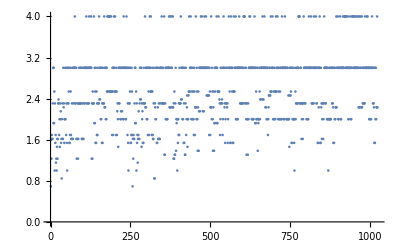

```mathematica
ListPlot[vals]
```

```mathematica
Select[vals,#<1&]
```

{9/13,11/13,9/13,11/13,11/13}

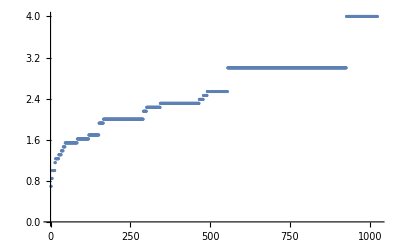

```mathematica
ListPlot[Sort[vals]]
```

```mathematica
Monitor[Table[k->Select[Experiment125[k],#<1&],{k,6,12}],k]
```

{6→{11/13,11/13,11/13,11/13,11/13},7→{8/17,15/17,14/17,15/17,15/17,15/17,15/17,16/17,16/17,15/17},8→{7/8,7/8,7/8},9→{9/13,11/13,9/13,11/13,11/13},10→{9/13,11/13,9/13,11/13,11/13},11→{8/17,15/17,14/17,13/17,15/17,15/17,15/17,16/17,16/17,15/17},12→{7/8,7/8,7/8,7/8,7/8,7/8,7/8}}

```mathematica
vals=Monitor[Table[{kkk,Min[Experiment125[kkk]]},{kkk,6,13}],kkk];Print[vals];ListLinePlot[vals]
```

$Aborted

## How do the graphs look

```mathematica
EdgeColor[eFull_,eLow_]:=Join[
Map[#->Directive[Darker[Green],Thick]&,Intersection[eFull,eLow]],
Map[#->Directive[Blue,Thick]&,SetDifference[eFull,eLow]],
Map[#->Directive[Red,Thick]&,SetDifference[eLow,eFull]]
]
```

```mathematica
ColorLabel[value_]:=If[value <1,Style[value,30,Red],Style[value,24,Darker[Green]]]
```

```mathematica
HowDotheGraphsLook[nodes_]:=Block[
{
lowerPatterns=Association[],
lowerGraph,
higherGraph,
higherPartitions=Association[],
efull,
elow
},
Table[
lowerPatterns[k]=First[QuadrilateralsWithPattern[nodes,k]];
higherPartitions[k]=Sort[Select[QuadrilateralsWithPattern[nodes+1,k],PartitionHasPattern[#,lowerPatterns[k]]&]]
,
{k,5}
];
lowerGraph=GraphForPartsLevel4[Values[lowerPatterns]];
elow=EdgeList[lowerGraph];
Map[Last,
Sort[
Flatten[
Table[
Table[
Table[
Table[
Table[
higherGraph=GraphForPartsLevel4[{part1,part2,part3,part4,part5}];
efull=EdgeList[higherGraph];
{ChromaticPolynomial[higherGraph,4]/ChromaticPolynomial[lowerGraph,4],
Labeled[
CompleteGraph[nodes+1,VertexLabels->"Name",EdgeStyle->EdgeColor[elow,efull],ImageSize->120],
ColorLabel[ChromaticPolynomial[higherGraph,4]/ChromaticPolynomial[lowerGraph,4]]
]
}
,
{part5,Take[higherPartitions[5],4]}
],
{part4,Take[higherPartitions[4],4]}
],
{part3,Take[higherPartitions[3],4]}
],
{part2,Take[higherPartitions[2],4]}
],
{part1,Take[higherPartitions[1],4]}
],
4]
]
]
]
```

```mathematica
HowDotheGraphsLook[6]//DeleteDuplicates
```

{-Graphics-11/13,-Graphics-11/13,-Graphics-11/13,-Graphics-1,-Graphics-16/13,-Graphics-17/13,-Graphics-17/13,-Graphics-17/13,-Graphics-17/13,-Graphics-19/13,-Graphics-19/13,-Graphics-20/13,-Graphics-20/13,-Graphics-20/13,-Graphics-20/13,-Graphics-21/13,-Graphics-21/13,-Graphics-21/13,-Graphics-22/13,-Graphics-22/13,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-2,-Graphics-29/13,-Graphics-29/13,-Graphics-30/13,-Graphics-30/13,-Graphics-30/13,-Graphics-30/13,-Graphics-32/13,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-3,-Graphics-4}

```mathematica
HowDotheGraphsLook[7]//DeleteDuplicates//Length
```

68

```mathematica
Monitor[Table[HowDotheGraphsLook[k]//DeleteDuplicates//Length,{k,6,10}],k]
```

{41,68,101,61,61}

```mathematica
Monitor[Table[HowDotheGraphsLook[k]//DeleteDuplicates//Length,{k,11,11}],k]
```

{87}

```mathematica
$HistoryLength=5
```

5

```mathematica
Monitor[Table[With[{res=HowDotheGraphsLook[k]//DeleteDuplicates//Length},
Print[res];res],{k,5,13}],k]
```

26

41

68

101

61

61

87

131

94

{26,41,68,101,61,61,87,131,94}

```mathematica
HowDotheGraphsLook[5]//DeleteDuplicates
```